# Actin Modeling

Authors: Matthew Hur and Dr. Eric Mjolsness, 2025 January 27
This is a dynamical graph grammar (DGG) model of the morphodynamics of the synaptic spine head built for actin network remodeling and biomechanics.

## Loading Plenum

```mathematica
<<Plenum.m
```

Plenum: version 24

## Defining The Problem

### User Defined Variables

```mathematica
nCG=25;
biomechanicalRate=1024;
membraneRate=1024;
```

### Variable Rules

```mathematica
boundarySpineRate=10^24;
eps=10^-10;
rateVars={spineFactor->membraneRate ,membraneFactor->membraneRate,boundarySpineFactor->boundarySpineRate,networkFactor->biomechanicalRate};
potentialVars={l0->1.,ϵ->0.875,hessianScaling->1./Sqrt[biomechanicalRate],vertexMin->1.5,overgrowthL->1.5};
```

### Basic Definitions

There are four types of ends which we use to apply specific rules to only actins of those types:

```mathematica
INT = 0.; (* internal monomer *)
POI = 1.; (* monomer at the pointed end *)
BAR = 2.; (* monomer at the barbed end *)
CAP = 3.; (* capping agent *)
POIMEM=4.;
BARMEM=5.;
CAPMEM=6.;
```

Codes for specific IDs for no connection - basically null pointers

```mathematica
aIDFreeP = -10000.; (* constant for the empty space at the pointed end of a monomer *)
aIDFreeB = -20000.; (* constant for the empty space at the barbed end of a monomer *)
arpIDFree = -30000.; (* arp free *)
membraneIDFree=-1.; (*ID for actins not attached to the membrane*)
```

We allow actins to be attached to either ATP or ADP, both when they exist in free globular form (G-Actin) and when they are attached to filaments (F-Actin).

We also model the parallel mechanism of activation of Arp2/3:
-Graphics-
In order to accomplish this, we have IDs for Arp2/3 whether it is activated (A_2) or deactivated (A_1).

```mathematica
ARPACTID=-1.;
ARPDEACTID=-2.;
```

The following is the initial condition input into Plenum software to test grammars following the grammar definition in each section.

```mathematica
myicReduced = ( {
actin[1,{ 0, 0}, aIDFreeP, 2, 0.0, 0, arpIDFree, POI,membraneIDFree,nCG,0,0,0],(* new node at the pointed end *)
actin[2, {1, 0.05}, 1, 3,0, 0, 4, INT,membraneIDFree,0,nCG-1,0,1.], (* new internal node *)
actin[3, {2, 0.}, 2, aIDFreeB, 0.0, 0, arpIDFree,BAR,membraneIDFree,nCG,0,0,0], (* new node at the pointed end *)

(* place a branch to begin with and see how it works *)
actin[4, {1 + Cos[70 Degree], Sin[70 Degree]}, 2, 5,0.,0.0,arpIDFree,INT, membraneIDFree,nCG,0,0,0],
actin[5, {1 + 2 Cos[70 Degree],2Sin[70 Degree]}, 4, aIDFreeB, 0.0, 0.0, arpIDFree, BAR,membraneIDFree,nCG,0,0,0],

newID[11], (* counter for new ids to be generated *)
arpCount[initArpNum], (* counter for the amount of ARP floating in the system at any given point in the sim *)
actinATPCount[initActinATPNum-5*nCG],
actinADPCount[initActinADPNum],
cofilinCount[initCofilinNum],
spineHeadArea[area],
cappingCount[initCappingNum],
camCount[initCamNum]
}/.{area->π (spineHeadRadius/actinObjectRise)^2/5})//N;
```

Here are IDs representing what type of information is stored at each position of an actin object.

```mathematica
ID = 1;
POS=2;
PREV = 3;
NEXT = 4;
ANGLE = 5;
CROSSLINKING=6;
BRANCH = 7;
TYPE = 8;
MEMBRANEBOUNDID=9;
ATPCount=10;(*ID for actin-ATP*)
ADPCount=11;(*ID for actin-ADP*)
ADPPiCount=12;(*ID for actin-ADP-Pi*)
(*IDs for Cofilin bindings*)
ADPCofCount=13;
```

### Constants

```mathematica
(**CONSTANTS**)

(*Dominguez R,Holmes KC.Actin structure and function.Annu Rev Biophys.2011;40:169-86. doi:10.1146/annurev-biophys-042910-155359. PMID:21314430;PMCID:PMC3130349.https://www.ncbi.nlm.nih.gov/pmc/articles/PMC3130349/Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC3130349/HyperlinkActionRecycledHyperlinkActive*)
actinMonomerRise=2.76 10^-9 (*m*) ;
actinObjectRise=actinMonomerRise nCG;

avogadros=6.022*10^23;
T=310;

θArp=70 (*degrees*)*π/180;

kB=1.38*10^-23(*J/K*)/actinObjectRise^2;
kBT=kB*T;

μ=42(*kg/mol*)/avogadros;
ω=Sqrt[κS/μ];
koff=10^6;(*Zero-mode waveguides visualize the first steps during gelsolin-mediated actin filament formationhttps://pubmed.ncbi.nlm.nih.gov/34896371/Nonehttps://pubmed.ncbi.nlm.nih.gov/34896371/HyperlinkActionRecycledHyperlinkActive*)
ϵUnit=-kBT Log[koff/ω]; (*Dissocation energy for a coarse-grained chain*)

κS=(0.1*10^-12/10^-9(*N/m*))( (200*10^-9)/actinMonomerRise);

σA=8.0*10^-9(*m*)/actinObjectRise; (*diameter of actin molecule*)
ρ=Sqrt[(κS/nCG)/(2ϵUnit)];

(*Measuring the flexural rigidity of actin filaments and microtubules from their thermal fluctuating shapes:A new perspective;PMCID:PMC24024.https://pubmed.ncbi.nlm.nih.gov/8432732/Nonehttps://pubmed.ncbi.nlm.nih.gov/8432732/HyperlinkActionRecycledHyperlinkActive*)
κB=((7.51*10^-26)(*Nm^2*)/actinObjectRise^3)(1/1.5 (*Tropomyosin correction*));
(*Myosin-I Synergizes with Arp2/3 Complex to Enhance Pushing Forces
of Branched Actin Networkshttps://pubmed.ncbi.nlm.nih.gov/39270022/Nonehttps://pubmed.ncbi.nlm.nih.gov/39270022/HyperlinkActionRecycledHyperlinkActive*)
κBArpFactor=2.;

(*Hunt AJ,Gittes F,Howard J.The force exerted by a single kinesin molecule against a viscous load.Biophys J.1994 Aug;67(2):766-81. doi:10.1016/S0006-3495(94)80537-5. PMID:7948690;PMCID:PMC1225420.https://www.ncbi.nlm.nih.gov/pmc/articles/PMC1225420/Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC1225420/HyperlinkActionRecycledHyperlinkActive*)
ζA[L_]:=Re[(4π η L)/(Log[L/σA]+0.886)];(*friction coefficient for actin*)
ζAPar[L_]:=Re[(2π η L)/(Log[L/σA]-0.114)];(*friction coefficient for actin*)
ζCam[L_]:=Re[(4π η L)/(Log[L/σCam]+0.886)];(*friction coefficient for cam*)
step[L_]:=1/(ζA[L]*biomechanicalRate)
stepCam[L_]:=1/(ζCam[L]*biomechanicalRate)
stepPar[L_]:=1/(ζAPar[L]*biomechanicalRate)


(*Gittes F,Mickey B,Nettleton J,Howard J.Flexural rigidity of microtubules and actin filaments measured from thermal fluctuations in shape.J Cell Biol.1993 Feb;120(4):923-34. doi:10.1083/jcb.120.4.923.PMID:8432732;PMCID:PMC2200075.https://pubmed.ncbi.nlm.nih.gov/8432732/Nonehttps://pubmed.ncbi.nlm.nih.gov/8432732/HyperlinkActionRecycledHyperlinkActive*)
Lp=17.7*10^-6(*m*)/actinObjectRise; (*persistence length of actin filament*)
θp=Sqrt[2/Lp];

(*Smith BA,Roy H,De Koninck P,Grütter P,De Koninck Y.Dendritic spine viscoelasticity and soft-glassy nature:balancing dynamic remodeling with structural stability.Biophys J.2007 Feb 15;92(4):1419-30. doi:10.1529/biophysj.106.092361.Epub 2006 Nov 17. PMID:17114228;PMCID:PMC1783894.https://www.ncbi.nlm.nih.gov/pmc/articles/PMC1783894/#fd3Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC1783894/#fd3HyperlinkActionRecycledHyperlinkActive*)
η=19.9/(2Pi)(*kg s/m*)*actinObjectRise; (*Newtonian viscosity of medium*)

(*Sanabria H,Swulius MT,Kolodziej SJ,Liu J,Waxham MN.{beta}CaMKII regulates actin assembly and structure.J Biol Chem.2009 Apr 10;284(15):9770-80. doi:10.1074/jbc.M809518200.Epub 2009 Feb 10. PMID:19208632;PMCID:PMC2665098. *)
σArp=(140+109+130)/3*10^-10(*m*);(*diameter of Arp2/3 Complex*)

speciesToMol=1/((10^3 4/3π((area*actinObjectRise^2 1/π)^(3/2)))avogadros);

(**KINETICS OF POLYMERIZATION**)

(*Selden LA,Kinosian HJ,Estes JE,Gershman LC.Impact of profilin on actin-bound nucleotide exchange and actin polymerization dynamics.Biochemistry.1999 Mar 2;38(9):2769-78. doi:10.1021/bi981543c.PMID:10052948.https://pubmed.ncbi.nlm.nih.gov/10052948/*Nonehttps://pubmed.ncbi.nlm.nih.gov/10052948/*HyperlinkActionRecycledHyperlinkActive*)
actinATPDissociation=0.08(*1/s*);
actinNucPhos=1.4(*1/s*);

(*Pollard TD.Rate constants for the reactions of ATP-and ADP-actin with the ends of actin filaments.J Cell Biol.1986 Dec;103(6 Pt 2):2747-54. doi:10.1083/jcb.103.6.2747.PMID:3793756;PMCID:PMC2114620.https://www.ncbi.nlm.nih.gov/pmc/articles/PMC2114620/Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC2114620/HyperlinkActionRecycledHyperlinkActive*)

kPlusBarbedT=11.6 10^6 (*1/(M s)*)*speciesToMol;
kMinusBarbedT=1.4 (*1/(s)*);
kPlusPointedT=1.3 10^6(*1/(M s)*)*speciesToMol;
kMinusPointedT=0.81(*1/(s)*);
kPlusBarbedD=3.8 10^6 (*1/(M s)*)*speciesToMol;
kMinusBarbedD=7.2 (*1/(s)*);
kPlusPointedD=0.16 10^6(*1/(M s)*)*speciesToMol;
kMinusPointedD=0.27(*1/(s)*);

fActinATPHydrolysis=0.3 (*1/s*);
gActinATPHydolysis=7*10^-6(*1/s*);

(**KINETICS OF ACTIN NETWORKS**)

(*Smith BA,Daugherty-Clarke K,Goode BL,Gelles J.Pathway of actin filament branch formation by Arp2/3 complex revealed by single-molecule imaging.Proc Natl Acad Sci U S A.2013 Jan 22;110(4):1285-90. doi:10.1073/pnas.1211164110.Epub 2013 Jan 4. PMID:23292935;PMCID:PMC3557048.https://www.ncbi.nlm.nih.gov/pmc/articles/PMC3557048/Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC3557048/HyperlinkActionRecycledHyperlinkActive*)

keqk2=3200*speciesToMol;
k1=19*speciesToMol;
kminus1=0.07;
kminus2=0.47;

(*Hayakawa K,Sekiguchi C,Sokabe M,Ono S,Tatsumi H.Real-Time Single-Molecule Kinetic Analyses of AIP1-Enhanced Actin Filament Severing in the Presence of Cofilin.J Mol Biol.2019 Jan 18;431(2):308-322. doi:10.1016/j.jmb.2018.11.010.Epub 2018 Nov 12. PMID:30439520;PMCID:PMC6507414. https://www.ncbi.nlm.nih.gov/pmc/articles/PMC6507414/*None https://www.ncbi.nlm.nih.gov/pmc/articles/PMC6507414/*HyperlinkActionRecycledHyperlinkActive*)

kcapon=2.3*10^6(*1/(M s)*)*speciesToMol;
kcapoff=9.5*10^-4(*1/s*);

(*Wioland H,Guichard B,Senju Y,Myram S,Lappalainen P,Jégou A,Romet-Lemonne G.ADF/Cofilin Accelerates Actin Dynamics by Severing Filaments and Promoting Their Depolymerization at Both Ends.Curr Biol.2017 Jul 10;27(13):1956-1967.e7.doi:10.1016/j.cub.2017.05.048.Epub 2017 Jun 15. PMID:28625781;PMCID:PMC5505867.https://pubmed.ncbi.nlm.nih.gov/28625781/Nonehttps://pubmed.ncbi.nlm.nih.gov/28625781/HyperlinkActionRecycledHyperlinkActive*)
kcofcapoff=3*10^-3(*1/s*);
kcofcapon=0.3*10^6(*1/(M s)*)*speciesToMol;


(*Khan S,Conte I,Carter T,Bayer KU,Molloy JE.Multiple CaMKII Binding Modes to the Actin Cytoskeleton Revealed by Single-Molecule Imaging.Biophys J.2016 Jul 26;111(2):395-408. doi:10.1016/j.bpj.2016.06.007.PMID:27463141;PMCID:PMC4968397.https://pubmed.ncbi.nlm.nih.gov/27463141/Nonehttps://pubmed.ncbi.nlm.nih.gov/27463141/HyperlinkActionRecycledHyperlinkActive*)

koffcamKIIβ=0.23 (*1/s*);
koncamKIIβ=0.5*10^6 (*1 / (M s)*)*speciesToMol;

(*Estimated using HullRad on AlphaFold PDB*)
camKIIβrad=26*10^-9(*nm*)/actinObjectRise; 
σCam=(camKIIβrad*2*6)/(2π)2;

(*BROWNIAN RATCHET*)

δ=2.7*10^-7*10^-2(*m*)/actinObjectRise;
ωoverf=δ/kBT;

(**SYNTHESIS AND DEGRADATION OF MOLECULES**)

(*Sialana FJ,Wang AL,Fazari B,Kristofova M,Smidak R,Trossbach SV,Korth C,Huston JP,de Souza Silva MA,Lubec G.Quantitative Proteomics of Synaptosomal Fractions in a Rat Overexpressing Human DISC1 Gene Indicates Profound Synaptic Dysregulation in the Dorsal Striatum.Front Mol Neurosci.2018 Feb 6;11:26. doi:10.3389/fnmol.2018.00026.PMID:29467617;PMCID:PMC5808171.https://pubmed.ncbi.nlm.nih.gov/29467617/Nonehttps://pubmed.ncbi.nlm.nih.gov/29467617/HyperlinkActionRecycledHyperlinkActive, Bonilla-Quintana M, Rangamani P. Biophysical modeling of actin-mediated structural plasticity reveals mechanical adaptation in dendritic spines. 2022 Nov 15. doi: 10.1101/2022.11.06.515372.https://pubmed.ncbi.nlm.nih.gov/38383589/Nonehttps://pubmed.ncbi.nlm.nih.gov/38383589/HyperlinkActionRecycledHyperlinkActive *)

bactSS=E^14.95951281;
actinDegRate=0.0081(*1/s*);
actinSynthRate=24.4284*10^-6(*M/s*)/speciesToMol;

arpcSS=E^5.596538302;
arpSynthRate=0.0255*10^-6(*M/s*)/speciesToMol;
arpDegRate=0.0013 (*1/s*);

cfl1SS=E^9.218833479;
cofilinSynthRate=0.0237*10^-6(*M/s*)/speciesToMol;
cofilinDegRate=0.0006(*1/s*); 

camk2bSS=E^12.55662979;
camk2bSSnum=actinSynthRate/actinDegRate camk2bSS/bactSS;
camSynthRate=0.00020944238775871162/60/speciesToMol(*species/s*);
camDegRate=0.7677386644519346/60(*1/s*); 

capzSS=E^6.697041512;
capzSSnum=arpSynthRate/arpDegRate capzSS/arpcSS;
cappingSynthRate=0.000014271505531589093/60/speciesToMol(*species/s*);
cappingDegRate=0.240757/60(*1/s*);

(*Roland J,Berro J,Michelot A,Blanchoin L,Martiel JL.Stochastic severing of actin filaments by actin depolymerizing factor/cofilin controls the emergence of a steady dynamical regime.Biophys J.2008 Mar 15;94(6):2082-94. doi:10.1529/biophysj.107.121988.Epub 2007 Dec 7. PMID:18065447;PMCID:PMC2257902.https://pubmed.ncbi.nlm.nih.gov/18065447/Nonehttps://pubmed.ncbi.nlm.nih.gov/18065447/HyperlinkActionRecycledHyperlinkActive*)
kATPHydrolysis=0.35 (*1/s*);
ksev=0.012(*1/s*);
kCofPiRelease=0.035 (*1/s*);
(*Carlier MF.Measurement of Pi dissociation from actin filaments following ATP hydrolysis using a linked enzyme assay.Biochem Biophys Res Commun.1987 Mar 30 143(3):1069-75. doi:10.1016/0006-291x(87)90361-5. PMID:3566755.https://pubmed.ncbi.nlm.nih.gov/3566755/Nonehttps://pubmed.ncbi.nlm.nih.gov/3566755/HyperlinkActionRecycledHyperlinkActive*)
kPiRelease=0.006(*1/s*); 

(*Wioland H,Guichard B,Senju Y,Myram S,Lappalainen P,Jégou A,Romet-Lemonne G.ADF/Cofilin Accelerates Actin Dynamics by Severing Filaments and Promoting Their Depolymerization at Both Ends.Curr Biol.2017 Jul 10;27(13):1956-1967.e7.doi:10.1016/j.cub.2017.05.048.Epub 2017 Jun 15. PMID:28625781;PMCID:PMC5505867.https://pubmed.ncbi.nlm.nih.gov/28625781/Nonehttps://pubmed.ncbi.nlm.nih.gov/28625781/HyperlinkActionRecycledHyperlinkActive*)
kOnCofEdge=17*10^6(*1/(M s)*)*speciesToMol ;
kOffCof=0.7(*1/s*);
kMinusBarbedCof=4.0(*1/s*);
kMinusPointedCof=3.3(*1/s*);

koffBEMax=30*10^6(*1/(M s)*)*speciesToMol;
KDADFbareBE=3.1*10^-6(*M*)/speciesToMol;

(*De La Cruz EM.How cofilin severs an actin filament.Biophys Rev.2009 May 15;1(2):51-59. doi:10.1007/s12551-009-0008-5. PMID:20700473;PMCID:PMC2917815.https://pubmed.ncbi.nlm.nih.gov/20700473/Nonehttps://pubmed.ncbi.nlm.nih.gov/20700473/HyperlinkActionRecycledHyperlinkActive*)
kOnSingleCof=10^4(*1/(M s*)*speciesToMol ;

(*Parameter Conversion*)

spineHeadVolume=4/3π (spineHeadRadius/10)^3 (*L*);

(**FACTORS**)
radiusInUnitLength=spineHeadRadius/actinObjectRise;
initActinNum=actinSynthRate/actinDegRate;
initActinATPNum=initActinNum;
initActinADPNum=initActinATPNum*actinATPDissociation/actinNucPhos;
initArpNum=arpSynthRate/arpDegRate;
initCofilinNum=(cofilinSynthRate/cofilinDegRate);
initCappingNum=(cappingSynthRate/cappingDegRate);
initCamNum=(camSynthRate/camDegRate);
```

### Curve-Fitting CamKIIβ and Aip1 (capping) Degradation Rates

(*Bosch M,Castro J,Saneyoshi T,Matsuno H,Sur M,Hayashi Y.Structural and molecular remodeling of dendritic spine substructures during long-term potentiation.Neuron.2014 Apr 16;82(2):444-59. doi:10.1016/j.neuron.2014.03.021.PMID:24742465;PMCID:PMC4281348.*)https://pubmed.ncbi.nlm.nih.gov/24742465/Nonehttps://pubmed.ncbi.nlm.nih.gov/24742465/HyperlinkActionRecycledHyperlinkActive

```mathematica
Export["~/Documents/aip1Data.csv",aip1Data]
```

~/Documents/aip1Data.csv

```mathematica
Export["~/Documents/camEstimatedData.csv",Table[{t,eq/.Join[nlm["BestFitParameters"],{mstar->camk2bSSnum*speciesToMol}]},{t,0,4,0.07}]]
```

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

~/Documents/camEstimatedData.csv

```mathematica
Export["~/Documents/aip1EstimatedData.csv",Table[{t,eq/.Join[nlm["BestFitParameters"],{mstar->camk2bSSnum*speciesToMol}]},{t,0,4,0.07}]]
```

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads nlm and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

ReplaceAll::reps: {Join[nlm[BestFitParameters],{mstar→0.000272804}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

~/Documents/aip1EstimatedData.csv

```mathematica
Export["~/Documents/aip1Data.csv",aip1Data]
```

~/Documents/aip1Data.csv

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

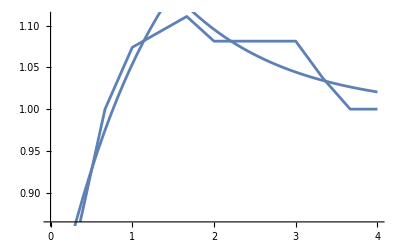

{influx→0.0000680964,km→0.767739,basal→0.000209442}

~/Documents/camEstimatedData.csv

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

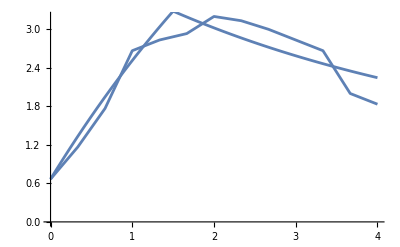

{influx→0.000117842,km→0.242064,basal→0.0000142715}

~/Documents/aip1EstimatedData.csv

```mathematica
camData={{0,1},{1/3,1.15},{2/3,1.35},{1,1.45},{4/3,1.475},{5/3,1.5},{2,1.46},{7/3,1.46},{8/3,1.46},{3,1.46},{10/3,1.4},{11/3,1.35},{4,1.35}};
camData[[;;,2]]/=1.35;
eq=(m[t]/.DSolve[{m'[t]==influx(HeavisideTheta[t]-HeavisideTheta[t-1.5])/mstar+km(1-m[t]),m[0]==camData[[1,2]]},m,{t,0,4}])[[1]];

nlm=NonlinearModelFit[camData,eq/.{mstar->camk2bSSnum*speciesToMol},{influx,km},t,Method->{NMinimize}];
Show[{ListLinePlot[camData],Plot[eq/.Join[nlm["BestFitParameters"],{mstar->camk2bSSnum*speciesToMol}],{t,0,4}]}]
Print[Join[nlm["BestFitParameters"],{basal->km*camk2bSSnum*speciesToMol}/.nlm["BestFitParameters"]]];
Export["~/Documents/camEstimatedData.csv",Table[{t,eq/.Join[nlm["BestFitParameters"],{mstar->camk2bSSnum*speciesToMol}]},{t,0,4,0.07}]]

aip1Data={{0,1},{1/3,1.75},{2/3,2.65},{1,4.0},{4/3,4.25},{5/3,4.4},{2,4.8},{7/3,4.7},{8/3,4.5},{3,4.25},{10/3, 4},{11/3,3},{4,2.75}};
aip1Data[[;;,2]]/=1.5;
eq=(m[t]/.DSolve[{m'[t]==influx(HeavisideTheta[t]-HeavisideTheta[t-1.5])/mstar+km(1-m[t]),m[0]==aip1Data[[1,2]]},m,{t,0,4}])[[1]];

nlm=NonlinearModelFit[aip1Data,eq/.{mstar->capzSSnum*speciesToMol},{influx,km},t,Method->{NMinimize}];
Show[{ListLinePlot[aip1Data],Plot[eq/.Join[nlm["BestFitParameters"],{mstar->capzSSnum*speciesToMol}],{t,0,4}]}]
Print[Join[nlm["BestFitParameters"],{basal->km*capzSSnum*speciesToMol}/.nlm["BestFitParameters"]]];
Export["~/Documents/aip1EstimatedData.csv",Table[{t,eq/.Join[nlm["BestFitParameters"],{mstar->capzSSnum*speciesToMol}]},{t,0,4,0.07}]]
```

### Definition of Rules

```mathematica
(* define rates for all of the reactions, change them here instead of hunting through all the rules *)
myRates ={ arpRate->arpSynthRate, cofilinRate->cofilinSynthRate,cofilinDeg->cofilinDegRate,barbGrowthT ->kPlusBarbedT/nCG,barbGrowthD ->kPlusBarbedD/nCG,barbRetr-> 1/(1/(kMinusBarbedT/(ATPCountCG+10^-8))+1/(kMinusBarbedD/(ADPCountCG+ADPPiCountCG+10^-8))+1/(kMinusBarbedCof/(ADPCofCountCG+10^-8))), pointGrowthT->kPlusPointedT/nCG,pointGrowthD->kPlusBarbedD/nCG, pointRetr->1/(1/(kMinusPointedT/(ATPCountCG+10^-8))+1/(kMinusPointedD/(ADPCountCG+ADPPiCountCG+10^-8))+1/(kMinusPointedCof/(ADPCofCountCG+10^-8))),cap->kcapon,capoff->kcapoff,sever->ksev, branchAng->θArp, sdGrowth->θp,arpDeg->arpDegRate ,actinRate->actinSynthRate ,actinDeg->actinDegRate ,bundle-> koncamKIIβ/nCG,unbundle-> koffcamKIIβ/nCG,actinPhos->actinNucPhos,actinATPDc->actinATPDissociation,cofBindEdge->kOnCofEdge,cofUnbind->kOffCof,cofBindSingle->kOnSingleCof,branchGrowthAct->keqk2*nCG,branchRetrAct->kminus2,branchGrowthDeact->k1/nCG,branchRetrDeact->kminus1/nCG,capRate->cappingSynthRate,capDeg->cappingDegRate,camRate->camSynthRate,camDeg->camDegRate,capoffcof->kcofcapoff,caponcof->kcofcapon};
```

```mathematica
(*Bonilla-Quintana M,Wörgötter F,Tetzlaff C,Fauth M.Modeling the Shape of Synaptic Spines by Their Actin Dynamics.Front Synaptic Neurosci.2020 Mar 10;12:9. doi:10.3389/fnsyn.2020.00009.PMID:32218728;PMCID:PMC7078677.https://www.frontiersin.org/articles/10.3389/fnsyn.2020.00009/fullNonehttps://www.frontiersin.org/articles/10.3389/fnsyn.2020.00009/fullHyperlinkActionRecycledHyperlinkActive*)
Pvar=85.7143 (*pN μm^-2*)*actinObjectRise;
tauvar=15(*pN μm^-1*)*10^-6;

kappavar=0.18(*pN μm*)*10^-12*10^-6/actinObjectRise^2;
ζ=0.002(*m/(s N)*)/actinObjectRise;
membraneRules={P->Pvar,tau->tauvar,kappa->kappavar,zeta->ζ/membraneFactor}/.{membraneFactor->membraneRate};
```

We also define a function for getting the relative position after rotation which works with vectorized coordinates.

```mathematica
newPos[oldPos_, angIn_] :=RotationTransform[angIn][oldPos];
```

## Visualizing The Actin Network

### Visualizer

This is the legend for visualizing actin networks:
- Circles: Actin objects
- Squares: Arp objects
- Triangles: Capping objects
- Hexagons: CamKIIβ objects
- Edge medium thickness indicates Actin-ATP and edge no thickness indicates Actin-ADP
- Opacity indicates degree of cofilin binding
- Color indicates bending angle

```mathematica
VisualizeActinSnapshot[initMoleculeList_, verbose_, energyMap_] := Module[{ml=initMoleculeList,viz, stack, pointCells, curCell, prevCell, color, prevPos, maxEnergy, minEnergy, energyFunc,vizLines,vizSpine,prevSpine,moleculeList,partnerCoords,shapeRadius=0.15,camObjects,curCam,spineCells,i},
(* initialize the stack and viz lists - using DFS to traverse the list of nodes *)
stack = {};
viz = {};
vizLines={};
vizSpine={Black};
camObjects=Cases[ml,cam[__]];
spineCells=Cases[ml,spine[_,_,_,_]];
moleculeList=DeleteCases[initMoleculeList,spine[__]];

For[i=1,i<=Length[spineCells],i++,
prevSpine=Cases[spineCells,spine[spineCells[[i,PREV]],__]][[1]];
AppendTo[vizSpine,Line[{spineCells[[i,POS]],prevSpine[[POS]]}]];
];
energyFunc[e_] := ColorData["TemperatureMap"][e^2/(π/4)];

For[i=1,i<=Length@camObjects,i++,
curCam=camObjects[[i]];
AppendTo[viz,{If[energyMap, energyFunc[curCam[[ANGLE]]],Black],RegularPolygon[curCam[[POS]],shapeRadius,6],Black}];
];

(* make an array of all the pointed ends *) 
pointCells = Join[Cases[moleculeList, actin[_, _, aIDFreeP, _, _,_,_, POI,_,_,_,_,_]],Cases[moleculeList, actin[_, _, aIDFreeP, _, _,_,_, POIMEM,_,_,_,_,_]]];

(* Iterate through all of the pointed ends *)
While[Length[pointCells] != 0,
curCell = pointCells[[1]];
pointCells = Drop[pointCells, 1];

(* draw circle for the first monomer - the pointed end *) 

AppendTo[viz, {If[energyMap, energyFunc[curCell[[ANGLE]]Boole[curCell[[NEXT]]!=aIDFreeB&&curCell[[PREV]]!=aIDFreeP]], Red],Disk[curCell[[POS]], shapeRadius]}];
If[verbose,AppendTo[viz, {Black, Text[ToString[Round[curCell[[ID]]]], curCell[[POS]]]}]];

If[curCell[[CROSSLINKING]]!=0,
AppendTo[viz,{Black,Line[{Select[camObjects,#[[ID]]==curCell[[CROSSLINKING]]&][[1]][[POS]],curCell[[POS]]}]}];
];
(* if there is a branch, draw the arp-actin and add the actin to the stack*)
If[curCell[[BRANCH]]>=0,Block[{curArp},
(* grab the arp-actin that is connected to this actin *)
curArp = Select[moleculeList,Head[#]===actin&&#[[1]]==curCell[[BRANCH]]&][[1]];
PrependTo[stack, {curCell,curArp, Black, curCell[[POS]]}];
]]; (* end if for checking the branch *)
If[curCell[[NEXT]] != aIDFreeB, PrependTo[stack, {curCell, Cases[moleculeList, actin[curCell[[NEXT]], _, _,  _, _,_,_,_,_,_,_,_,_]][[1]], Black, curCell[[POS]]}]];
(* Loop while the stack has elements in it *)
While[Length[stack] != 0,
(* grab the color, curCell, and prevCell from the top of the stack then delete the elem *)
prevCell = stack[[1, 1]];
curCell = stack[[1, 2]];
color = stack[[1, 3]];
prevPos = stack[[1, 4]];
(* draw the arrow from the current node to the previous node *)
PrependTo[vizLines, {Black, Line[{curCell[[POS]], prevPos}]}];
(** draw a triangle if it is a capping monomer, circle otherwise **)
If[curCell[[TYPE]]==CAP,
(* draw the triangle to represent the capping monomer *)
AppendTo[viz, {Black,Triangle[{{curCell[[POS]][[1]],curCell[[POS]][[2]]-shapeRadius}, curCell[[POS]]+{-newPos[{0,shapeRadius}, Pi / 3][[1]],newPos[{0,shapeRadius}, Pi / 3][[2]]},curCell[[POS]]+{ newPos[{0, shapeRadius}, Pi / 3][[1]],  newPos[{0, shapeRadius}, Pi / 3][[2]]}}]}],
(* draw the circle to represent the monomer *)
AppendTo[viz,{If[energyMap&&curCell[[NEXT]] == aIDFreeB,Green,energyFunc[curCell[[ANGLE]]]],Disk[curCell[[POS]], shapeRadius]}];
(* draw the cellID *)
If[verbose,AppendTo[viz, {Black,Text[ToString[Round[curCell[[ID]]]],curCell[[POS]]]}]];
];

stack = Drop[stack, 1];

If[curCell[[CROSSLINKING]]!=0,
AppendTo[viz,{Black,Line[{Select[camObjects,#[[ID]]==curCell[[CROSSLINKING]]&][[1]][[POS]],curCell[[POS]]}]}];
];
If[curCell[[BRANCH]] >=0.,Module[{curArp},
(* grab the arp that is connected to this actin *)
curArp = Select[moleculeList, Head[#]===actin&&#[[1]]==curCell[[BRANCH]]&][[1]];
(*add the branch's first actin to the stack*)
PrependTo[stack,{curCell,curArp,Black,curCell[[POS]]}];
]];
If[curCell[[NEXT]] != aIDFreeB, PrependTo[stack, {curCell, Cases[moleculeList, actin[curCell[[NEXT]], _,  _, _, _,_,_,_,_,_,_,_,_]][[1]], Black, curCell[[POS]]}]];
];
];
{Length[moleculeList],Flatten[Prepend[Prepend[viz,vizLines],vizSpine]], BarLegend[{"TemperatureMap", {0, 2}}]}];
```

```mathematica
(* function to grab a list of all the actin types from full simulation *)
makeMoleculeLists[simulationArray_] := 
Map[Join[Cases[{#}, actin[__]],Cases[{#}, spine[ __]],Cases[{#}, cam[ __]]] &, simulationArray]//Flatten
```

```mathematica
(* function to return graphics list for all snapshots in a sim *)
vizSim[simulationArray_, verbose_, energyMap_,n_:10,tmax_:0.] := Module[{vizList,dt,mLists,bbox,timePos,t,start,simList={}},
mLists = makeMoleculeLists/@simulationArray[[;;,2]];
bbox = {White,Rectangle[{Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]-2, Min[Map[#[[POS,2]]&, Flatten[mLists]]]-2}, {Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+2, Max[Map[#[[POS,2]]&, Flatten[mLists]]]+2}]};
timePos={(Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]])/2,Max[Flatten[Map[#[[POS,2]]&,#]&/@mLists]]+1};
simList=Transpose[{simulationArray[[;;,1]],mLists}];
vizList=Map[Graphics[Join[bbox,Append[VisualizeActinSnapshot[#[[2]],verbose,True][[2]],{Black,Text[Style["Time: "<>ToString[Round[(#[[1]]*1000)]/1000.]<>" secs.",Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]}]]//Flatten]&,simList]
];
sampleSim[directory_,dt_:0.005]:=
Module[{files,simList,maxTime,simNumbers,fgi,filegroups,simulationArray,t,sim,i,j,globString="simSpine*.wls"},
simList={};
files=directory<>"/"<>#<>".wls"&/@SortBy[FileBaseName[#]&/@FileNames[directory<>"/"<>globString],processFileNames];

simNumbers=Range[Length@filegroups];
simulationArray={};
t=0;
For[i=1,i<=Length@files,i+=1,
sim=Import[files[[i]]][[2]];
For[j=1,j<=Length@sim,j++,
If[sim[[j,1]]>=t,
AppendTo[simulationArray,sim[[j]]];
t+=dt;
]
]
];
simulationArray
]
```

```mathematica
animateGrowth[simulationArray_,verbose_:False] := Module[{mLists,bbox,timePos},
mLists = makeMoleculeLists/@simulationArray[[;;,2]];
bbox = {White,Rectangle[{Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]-2, Min[Map[#[[POS,2]]&, Flatten[mLists]]]-2}, {Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+2, Max[Map[#[[POS,2]]&, Flatten[mLists]]]+2}]};
timePos={(Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]])/2,Max[Flatten[Map[#[[POS,2]]&,#]&/@mLists]]+1};
frames=Map[Show[{Graphics[Join[bbox,Append[VisualizeActinSnapshot[#[[2]],verbose,True][[2]],{Black,Text[Style["Time: "<>ToString[#[[1]]]<>", Frame: "<>ToString[#[[3]]],Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]}]//Flatten]]}]&, Transpose[{#[[1]]&/@simulationArray,mLists,Range[Length@simulationArray]}]];
ListAnimate[frames]
];

processFileNames[name_]:=
ToExpression@StringDelete[name,LetterCharacter]

animateGrowthDirectory[directory_,globString_,outDir_,dt_:0.005] := Module[{start,simList={},t,mLists,bbox,timePos,files,lastFrame,i,j,frameNumber,frames,simulationArray},
files=SortBy[FileBaseName[#]&/@FileNames[directory<>globString],processFileNames];
files=directory<>#<>".wls"&/@files;

simulationArray={};

For[i=1,i<=Length@files,i+=1,
simulationArray=Join[simulationArray,Import[files[[i]]][[2;;]]];
];
simulationArray=simulationArray/.{}->Nothing;

For[i=1,i<=Length@simulationArray,i+=1,
AppendTo[simList,simulationArray[[i]]];
];
mLists = makeMoleculeLists[#]&/@simList;
bbox = {White,Rectangle[{Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]-2, Min[Map[#[[POS,2]]&, Flatten[mLists]]]-2}, {Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+2, Max[Map[#[[POS,2]]&, Flatten[mLists]]]+2}]};
timePos={(Max[Flatten[Map[#[[POS,1]]&,#]&/@mLists]]+Min[Flatten[Map[#[[POS,1]]&,#]&/@mLists]])/2,Max[Flatten[Map[#[[POS,2]]&,#]&/@mLists]]+1};
simList=Transpose[{Range[0,Length@mLists-1]*dt,mLists}];
CreateDirectory[outDir];
frameNumber=0;
frames=Map[Graphics[Join[bbox,Append[VisualizeActinSnapshot[#[[2]],False,True][[2]],{Black,Text[Style["Time: "<>ToString[#[[1]]]<>" s.",Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]}]]//Flatten]&,simList];
For[j=1,j<=Length@frames,j++,
frameNumber++;
Export[outDir<>"frame_"<>IntegerString[frameNumber,10,8]<>".png",frames[[j]]];
];
];

animateGrowthDirectorySet[directory_,globString_,outDir_,dt_:0.0005] := Module[{simList,start,t,mLists,bbox,timePos,files,end,lastFrame,frames,simulationArray,frame,groupfiles,filegroups,fgi,maxTime,simSubList,xs,ys,maxis,simNumbers,i,j,sim},
simList={};
groupfiles=FileNames[directory];
groupfiles=DeleteCases[groupfiles,DirectoryName[directory]<>".DS_Store"];
filegroups={};
For[i=1,i<=Length@groupfiles,i++,
AppendTo[filegroups,(groupfiles[[i]]<>"/"<>#<>".wls"&/@SortBy[FileBaseName[#]&/@FileNames[groupfiles[[i]]<>"/"<>globString],processFileNames])];
];

maxTime=Max[Import[#[[-1]]][[2,-1,1]]&/@filegroups];
simList={};
progressbar=StringRepeat["|",1]<>StringRepeat[" ",Length@filegroups-1]<>"|";
Print[Dynamic[progressbar]];
simNumbers=Range[Length@filegroups];
For[fgi=1,fgi<=Length@filegroups,fgi++,
files=filegroups[[fgi]];
simulationArray={};
t=0;
For[i=1,i<=Length@files,i+=1,
sim=Import[files[[i]]][[2]];
For[j=1,j<=Length@sim,j++,
If[sim[[j,1]]>=t,
AppendTo[simulationArray,sim[[j,2]]];
t+=dt;
]
]
];
AppendTo[simList,simulationArray];
progressbar=StringRepeat["|",fgi]<>StringRepeat[" ",Length@filegroups-fgi]<>"|";
];
mLists = makeMoleculeLists/@#&/@simList;
xs=#[[1]]&/@Select[#[[POS]]&/@Flatten[mLists],ListQ];
ys=#[[2]]&/@Select[#[[POS]]&/@Flatten[mLists],ListQ];
bbox = {White,Rectangle[{Min[xs]-2, Min[ys]-2}, {Max[xs]+2, Max[ys]+2}]};
timePos={(Max[xs]+Min[xs])/2,Max[ys]+1};

simList=Transpose@{Range[0,Length@#]&/@mLists,mLists};
maxis=Length@#&/@mLists;
CreateDirectory[outDir];

Do[frame=GraphicsGrid[Partition[(Graphics[Join[bbox,(VisualizeActinSnapshot[simList[[#]][[2]][[Min[{maxis[[#]],frameN+1}]]],False,True][[2]]),{Black,Text[Style["Time: "<>ToString[simList[[#]][[1]][[Min[{maxis[[#]],frameN+1}]]]*dt]<>" s.",Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]}]]&/@Range[1,Length@filegroups]),(QuotientRemainder[Length@filegroups,2][[2]]+1)//UpTo]//Transpose,Frame->All];Export[outDir<>"frame_"<>IntegerString[frameN,10,8]<>".png",frame];,{frameN,0,Max@maxis}];
];
```

### Plotting

```mathematica
plotSim[simulationArray_,slices_:1] := Module[{totalActin=Map[{#[[1]], Length[Select[#[[2]], Head[#]===actin&]]*nCG+Cases[#[[2]],actinATPCount[_]][[1,1]]+ Cases[#[[2]], actinADPCount[_]][[1, 1]]} &, simulationArray[[1;;Length@simulationArray;;slices]]],SA=simulationArray[[1;;Length@simulationArray;;slices]],data},
data={
Map[{#[[1]], Length[Select[#[[2]], Head[#]===actin&]]*nCG} &, SA],
Map[{#[[1]], Total[If[Head[#]===actin,#[[ATPCount]],0]&/@#[[2]]]} &, SA],
Map[{#[[1]], Total[If[Head[#]===actin,#[[ADPCount]],0]&/@#[[2]]]+Total[If[Head[#]===actin,#[[ADPCofCount]],0]&/@#[[2]]]+Total[If[Head[#]===actin,#[[ADPPiCount]],0]&/@#[[2]]]} &, SA],
Map[{#[[1]],Total[If[Head[#]===actin,#[[ADPCofCount]],0]&/@#[[2]]]} &, SA],
Map[{#[[1]], Cases[#[[2]], actinATPCount[_]][[1, 1]]+ Cases[#[[2]], actinADPCount[_]][[1, 1]]} &, SA],
totalActin,
Map[{#[[1]], Cases[#[[2]],actinATPCount[_]][[1,1]]} &, SA],
Map[{#[[1]], Cases[#[[2]], actinADPCount[_]][[1, 1]]} &, SA]};
ListLinePlot[data,PlotLegends -> {"Polymerized Actin","Polymerized Actin-ATP","Polymerized Actin-ADP",  "Bound Cofilin", "Free Actin","Total Actin","G-Actin-ATP","G-Actin-ADP"},PlotRange->{{simulationArray[[1,1]],simulationArray[[-1,1]]},{0,Max[totalActin]}},Frame->True,FrameLabel->{"Time (s)", "Actin Molecule Number"},PlotLabel->"Plot of Number of Molecules"]
]
```

## Molecule Rules

Here we define the rules that govern the changes in the number of free molecules without a change in the actin network structure. There is one rule that changes the type of bound nucleotide to actins in filaments. We have ARP synthesis and degradation, actin synthesis and degradation, actin-ADP and actin-ATP dissociation, F-Actin hydrolysis (conversion of F-actin-ATP to F-actin-ADP).

```mathematica
(* rules for ARP synthesizing and degrading *)
rulesMolVanilla = {
(* ARP synthesis *)
{arpCount[numArp],spineHeadArea[area]} -> {arpCount[numArp],spineHeadArea[area]},
solving[numArp'==arpRate Boole[numArp>0]],

(* ARP degradation *)
(arpCount[numArp] -> arpCount[numArp]),
solving[numArp'==-arpDeg *numArp  Boole[numArp>0]],

(* Cap synthesis *)
{cappingCount[numCap],spineHeadArea[area]} -> {cappingCount[numCap],spineHeadArea[area]},
solving[numCap'==capRate],

(* Cap degradation *)
(cappingCount[numCap] -> cappingCount[numCap ]),
solving[numCap'==-capDeg *numCap  Boole[numCap>0]],

(* Cam synthesis *)
{camCount[numCam],spineHeadArea[area]} -> {camCount[numCam],spineHeadArea[area]},
solving[numCam'==camRate],

(* Cam degradation *)
(camCount[numCam] -> camCount[numCam]),
solving[numCam'==-camDeg *numCam  Boole[numCam>0]],

(* Cofilin synthesis *)
{cofilinCount[numCofilin],spineHeadArea[area]} -> {cofilinCount[numCofilin],spineHeadArea[area]},
solving[numCofilin'==cofilinRate],

(* Cofilin degradation *)
(cofilinCount[numCofilin] -> cofilinCount[numCofilin]),
solving[numCofilin'==-cofilinDeg *numCofilin  Boole[numCofilin>0]],

(* Actin synthesis *)
{actinATPCount[numActin],spineHeadArea[area]} -> {actinATPCount[numActin],spineHeadArea[area]},
solving[numActin'==actinRate],

(* Actin degradation *)
({actinATPCount[numActin] ,spineHeadArea[area]}->{ actinATPCount[numActin],spineHeadArea[area]}),
solving[numActin'==-actinDeg *numActin  Boole[numActin>0]],

{actinADPCount[numActin] ,spineHeadArea[area]}->{actinADPCount[numActin],spineHeadArea[area]},
solving[numActin'==-actinDeg *numActin  Boole[numActin>0]]
};
rulesNuc={
(*Hydrolysis of F-Actin-Nucleotides*)
{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineHeadArea[area]}->{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG-1,ADPCountCG,ADPPiCountCG+1,ADPCofCountCG],spineHeadArea[area]},with[kATPHydrolysis Boole[ATPCountCG>=1]ATPCountCG],
{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineHeadArea[area]}->{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG,ADPCountCG+1,ADPPiCountCG-1,ADPCofCountCG],spineHeadArea[area]},with[kPiRelease Boole[ADPPiCountCG>=1]ADPPiCountCG],

{a1==actin[aID, coords,aIDP, aIDNext, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[aIDNext, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineHeadArea[area]}->{a1,actin[aIDNext, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN+1,ADPPiCountCGN-1,ADPCofCountCGN],spineHeadArea[area]},with[Boole[ADPCofCountCG>0]kCofPiRelease ADPPiCountCGN],
{actin[aID, coords,aIDP, aIDNext, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],aN==actin[aIDNext, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineHeadArea[area]}->{aN,actin[aID, coords,aIDP, aIDNext, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG+1,ADPPiCountCG-1,ADPCofCountCG],spineHeadArea[area]},with[Boole[ADPCofCountCGN>0] kCofPiRelease ADPPiCountCG],

{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineHeadArea[area]}->{actin[aID,coords, aIDP, NID,randAng,clID, arpID, type,membraneID,ATPCountCG,ADPCountCG+1,ADPPiCountCG-1,ADPCofCountCG],spineHeadArea[area]},with[kCofPiRelease Boole[ADPPiCountCG>0&&ADPCofCountCG>0]ADPPiCountCG],


(*Break rods that are really bent*)
{actin[aIDP, coordsP,aIDPP, aID, angleP,clIDP, arpIDP, INT,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID, coords,aIDP, aIDNext, angle,clID, arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]}->{
actin[aIDP, coordsP,aIDPP, aIDFreeB, 0.,clIDP, arpIDP, BAR,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID, coords,aIDFreeP, aIDNext, 0.,clID, arpID, POI,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]},
with[boundarySpineFactor Boole[Norm[coordsP-coords]>overgrowthL||Abs@angle>45 Degree||Abs@angleP>45Degree]]};
```

## Barbed End Rules

```mathematica
rulesBarb={

(**** elongation at the barbed end ****)
(* Will destroy the current end and make two new nodes, one to recreate the current end and one to add a new node *)
(** growing in a straight line with the previous being an actin **)
(* X -> actinP -> actinEnd -> newActinEnd *)
(*Rule for elongating in the presence of free actin-ATP*)

{aP == actin[aIDP, coordsP, aIDPP, aIDPN,angleP, clIDP, arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords, aIDP,   aIDFreeB,angle,clID, arpID, BAR,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area]
} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[aID,coords, aIDP, NID,randAng,clID, arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(* make the newly created end node *)
actin[NID, coords+newPos[coords-coordsP, randAng]/Norm[coords-coordsP],aID, aIDFreeB,angle,0.0,arpIDFree, BAR,membraneIDFree,nCG,0.0,0.0,0.0] 
},
with[barbGrowthT numActin* grammarPDF[NormalDistribution[0.0, sdGrowth], randAng]],

(*Rule for elongating when previous actin in the presence of free actin-ADP*)
{aP == actin[aIDP, coordsP, aIDPP, aIDPN,angleP, clIDP, arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords, aIDP,   aIDFreeB,angle,clID, arpID, BAR,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area]} -> {
actinADPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[aID,coords, aIDP, NID,randAng,clID, arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(* make the newly created end node *)
actin[NID, coords+newPos[coords-coordsP, randAng]/Norm[coords-coordsP],aID,aIDFreeB,0.0,0.0,arpIDFree, BAR,membraneIDFree,0.0,nCG,0.0,0.0] 
},
with[barbGrowthD numActin*grammarPDF[NormalDistribution[0.0, sdGrowth], randAng]],

(**** retraction at the barbed end ****)
(** remove one actin when the previous is an actin, removal of an actin  **)
(* X -> newActinEnd -> oldActinEnd *)

{actin[aID, coords, aIDP, aIDFreeB,angle, 0.0,arpID, BAR,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], 
actin[aIDP, coordsP, aIDPP, aID,angleP, 0.0,arpIDP,INT,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actinATPCount[numActinATP],cofilinCount[numCofilin],actinADPCount[numActinADP],
spineHeadArea[area]
} -> 
{
actinATPCount[numActinATP+ATPCountCG],
actinADPCount[numActinADP+ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
spineHeadArea[area],
actin[aIDP,coordsP,aIDPP,aIDFreeB,0.0,0.0,arpIDP,BAR,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[barbRetr Boole[arpID==arpIDFree]Boole[aIDPP!=aIDFreeP]],
{actin[aID, coords, aIDP, aIDFreeB,angle, 0.0,arpID, BARMEM,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], 
actin[aIDP, coordsP, aIDPP, aID,angleP, 0.0,arpIDP,INT,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actinATPCount[numActinATP],actinADPCount[numActinADP],cofilinCount[numCofilin],
spineHeadArea[area],spineAtt[aID,sp0,sp1]
} -> 
{
actinATPCount[numActinATP+ATPCountCG],
actinADPCount[numActinADP+ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
spineHeadArea[area],
actin[aIDP,coordsP,aIDPP,aIDFreeB,0.0,0.0,arpIDP,BAR,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[barbRetr Boole[arpID==arpIDFree]Boole[aIDPP!=aIDFreeP]],

(* allow actin monomers to bind and unbind with new arp complexes *)
(* actin bind to arp *)
{aP ==actin[aIDP, coordsP, aIDPP, aIDPN,angleP,clIDP,arpID, INT,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID, coords, aIDP, aIDNN,angle,clID,ARPACTID, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
newID[NID],actinATPCount[numActin],spineHeadArea[area]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new arp *)
actin[aID, coords, aIDP, aIDNN,angle,clID,NID, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(* make the newly created end node *)
actin[NID, coords+newPos[coords-coordsP, θArp (1-2Boole[branchSide>0.5])]/Norm[coords-coordsP], aID, aIDFreeB,0.0,0.0,arpIDFree,BAR,membraneIDFree,nCG,0.0,0.0,0.0]
},
with[Boole[numActin>nCG]barbGrowthT*numActin * grammarPDF[UniformDistribution[{0, 1}], branchSide]Boole[type!=CAP]],

(* actin unbinding from the arp complex if it is the last monomer and has no branches from it *)
{actin[arpPrev, coordsP, aIDP, aIDN,angleP, clIDP,aID, type,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, arpPrev, aIDFreeB,angle, 0.0,arpID, BAR,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actinATPCount[numActinATP],actinADPCount[numActinADP],cofilinCount[numCofilin],
spineHeadArea[area],arpCount[numArp]} -> {
arpCount[numArp+Boole[arpID!=arpIDFree]],
actinATPCount[numActinATP+ATPCountCG],
actinADPCount[numActinADP+ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
(* recreate the arp complex and have it point to empty space *)
actin[arpPrev, coordsP, aIDP, aIDN,angleP, clIDP,ARPACTID, type,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineHeadArea[area]
},
with[barbRetr Boole[arpID<0]],
{actin[arpPrev, coordsP, aIDP, aIDN,angleP, clIDP,aID, type,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, arpPrev, aIDFreeB,angle, 0.0,arpID, BARMEM,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actinATPCount[numActinATP],actinADPCount[numActinADP],
spineHeadArea[area],spineAtt[aID,sp0,sp1],arpCount[numArp],cofilinCount[numCofilin]} -> {
arpCount[numArp+Boole[arpID!=arpIDFree]],
spine[membraneID,sCoords,sIDP,sIDN,membraneIDFree,centralID1,centralID3],
actinATPCount[numActinATP+ATPCountCG],
actinADPCount[numActinADP+ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
(* recreate the arp complex and have it point to empty space *)
actin[arpPrev, coordsP, aIDP, aIDN,angleP, clIDP,ARPACTID, type,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineHeadArea[area]
},
with[barbRetr Boole[arpID<0]]
};
```

## Pointed End Rules

```mathematica
(* rules for model b *)
rulesPoint := {
(* elongation at the pointed end *)
(* identical in many ways to the barbed end elongation*)
{aP ==actin[aIDN, coordsN, aID,aIDNN,angleN,clIDP,arpIDN,typeN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],actin[aID, coords, aIDFreeP, aIDN,angle, clID, arpID, POI,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], newID[NID],actinATPCount[numActin],
spineHeadArea[area]} -> {
actinATPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aP,
(* recreate the current node as a INT *)
actin[aID, coords, NID, aIDN,-randAng,clID,arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(* make the new node at the pointed end *)
actin[NID,coords+newPos[coords-coordsN, randAng]/Norm[coords-coordsN], aIDFreeP, aID,0.0, 0.0, arpIDFree, POI,membraneIDN,nCG,0.0,0.0,0.0] (* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]pointGrowthT  numActin*grammarPDF[NormalDistribution[0.0, sdGrowth], randAng]],
(*Rule for elongating in the presence of free actin-ADP*)
{aP ==actin[aIDN, coordsN, aID,aIDNN,angleN,clIDP,arpIDN,typeN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],actin[aID, coords, aIDFreeP, aIDN,angle, clID, arpID, POI,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], newID[NID],actinADPCount[numActin],
spineHeadArea[area]} -> {
actinADPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aP,
(* recreate the current node as a INT *)
actin[aID, coords, NID, aIDN,-randAng,clID,arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(* make the new node at the pointed end *)
actin[NID,coords+newPos[coords-coordsN, randAng]/Norm[coords-coordsN], aIDFreeP, aID,0.0, 0.0, arpIDFree, POI,membraneIDN,0.0,nCG,0.0,0.0] (* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]pointGrowthD numActin grammarPDF[NormalDistribution[0.0, sdGrowth], randAng]],
(* retraction at the pointed end *)

{actin[aID,coords, aIDFreeP, aIDN,angle, 0.0,arpID, POIMEM,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsN, aID, aIDNN,angleN, 0.0,arpIDN, INT,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],actinATPCount[numATPActin],cofilinCount[numCofilin],
actinADPCount[numADPActin],
spineHeadArea[area],spineAtt[aID,sp0,sp1]} -> {
spineHeadArea[area],
actinATPCount[numATPActin+ATPCountCG],
actinADPCount[numADPActin+ ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
(* change the next node so that the current POI is dropped *)
actin[aIDN, coordsN, aIDFreeP, aIDNN,0.0, 0.0, arpIDN, POI,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
},
with[pointRetr Boole[arpID==arpIDFree]Boole[aIDNN!=aIDFreeB]],
{actin[aID,coords, aIDFreeP, aIDN,angle, 0.0,arpID, POI,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsN, aID, aIDNN,angleN, 0.0,arpIDN, INT,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],actinATPCount[numATPActin],cofilinCount[numCofilin],
actinADPCount[numADPActin],
spineHeadArea[area]} -> {
spineHeadArea[area],
actinATPCount[numATPActin+ATPCountCG],
actinADPCount[numADPActin+ ADPCountCG+ADPPiCountCG+ADPCofCountCG],
cofilinCount[numCofilin+ADPCofCountCG],
(* change the next node so that the current POI is dropped *)
actin[aIDN, coordsN, aIDFreeP, aIDNN,0.0, 0.0, arpIDN, POI,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
},
with[pointRetr Boole[arpID==arpIDFree]Boole[aIDNN!=aIDFreeB]]
};
```

## Branching Rules

```mathematica
(* rules for model D *)
rulesBranch = {
(* arp binding to open actin monomer *)
{actin[aID, coords, aIDP, aIDN,angle, clID, arpIDFree, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],  arpCount[numArp],actinATPCount[numActin],
spineHeadArea[area]} -> {
(* update the arpcount variable *)
arpCount[numArp - 1],
actinATPCount[numActin-1],
(* re-create the current actin monomer and have it point to the new arp protein *)
actin[aID, coords, aIDP, aIDN,angle,clID, ARPACTID, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area]
},
with[Boole[numArp>1]Boole[numActin>1]numArp*branchGrowthAct],

(* arp unbinding from an actin monomer - only if it does not have actin attached to it *)
{actin[aID, coords, aIDP, aIDN,angle, clID,ARPACTID, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], arpCount[numArp],
spineHeadArea[area]} -> {
(* increase the floating arp counter *)
arpCount[numArp + 1],
(* recreate the actin on the parent strand *)
actin[aID, coords, aIDP, aIDN,angle, clID,arpIDFree, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area]
},
with[branchRetrAct],
{actin[aID, coords, aIDP, aIDN,angle, clID, arpIDFree, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG], arpCount[numArp],
spineHeadArea[area]} -> {
(* update the arpcount variable *)
arpCount[numArp - nCG],
(* re-create the current actin monomer and have it point to the new arp protein *)
actin[aID, coords, aIDP, aIDN,angle,clID, ARPDEACTID, type,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area]
},
with[Boole[numArp>nCG]numArp*branchGrowthDeact],

(* arp unbinding from an actin monomer - only if it does not have actin attached to it *)
{actin[aID, coords, aIDP, aIDN,angle, clID,ARPDEACTID, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],arpCount[numArp],
spineHeadArea[area]} -> {
(* increase the floating arp counter *)
arpCount[numArp + nCG],
(* recreate the actin on the parent strand *)
actin[aID, coords, aIDP, aIDN,angle, clID,arpIDFree, type,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area]
},
with[branchRetrDeact]
};
```

## Capping Rules

```mathematica
rulesCap := {
(* add a capping node to the end of a filament *)
{actin[aID, coords, aIDP, aIDFreeB, angle,clID, arpID, BAR,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],cappingCount[capNum],spineHeadArea[area]}->{
(* add back the current end node pointing to the cap node as an internal monomer *)
actin[aID,coords, aIDP, aIDFreeB,  angle,clID, arpID, CAP,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area],
cappingCount[capNum-1]
},
with[If[ADPCofCountCG<nCG/2,cap,caponcof]*capNum ],
{actin[aID, coords, aIDP, aIDFreeB, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],cappingCount[capNum]}->{
actin[aID, coords, aIDP, aIDFreeB, angle,clID, arpID, Boole[end==CAP]BAR+Boole[end==CAPMEM]BARMEM,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],cappingCount[capNum+1]
},
with[If[ADPCofCountCG<nCG/2,capoff,capoffcof]Boole[end==CAP||end==CAPMEM]]
};
```

## Severing Rules

```mathematica
rulesCof := {
(*Bind and unbind Cofilin to actin-ADP*)
{
actin[aID, coords,aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[aID, coords, aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG-1,ADPPiCountCG,ADPCofCountCG+1],
cofilinCount[numCofilin-1],spineHeadArea[area]
},
with[cofBindSingle*ADPCountCG*numCofilin Boole[ADPCountCG>0&&ADPCofCountCG<nCG]],

{
actin[aID, coords,aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[aID, coords, aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG-1,ADPPiCountCG,ADPCofCountCG+1],
cofilinCount[numCofilin-1],spineHeadArea[area]
},
with[cofBindEdge ADPCountCG*numCofilin Boole[ADPCountCG>0]],
{
actin[aID, coords,aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[aID, coords, aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG+1,ADPPiCountCG,ADPCofCountCG-1],
cofilinCount[numCofilin+1],spineHeadArea[area]
},
with[(ADPCofCountCG)cofUnbind Boole[ADPCountCG>0]],

(*Accelerated bind cofilin*)
{
a1==actin[aID, coords,aIDP, aIDPN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[aIDN, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN-1,ADPPiCountCGN,ADPCofCountCGN+1],
cofilinCount[numCofilin-1],a1,spineHeadArea[area]
},
with[Boole[ADPCofCountCG==nCG&&ADPCofCountCGN==0]cofBindEdge ADPCountCGN*numCofilin Boole[ADPCountCGN>0]],

{
actin[aIDP, coordsP,aIDPP, aIDPN, angleP, clIDP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], 
a1==actin[aID, coords,aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[aIDP, coordsP,aIDPP, aIDPN, angleP, clIDP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP-1,ADPPiCountCGP,ADPCofCountCGP+1], 
cofilinCount[numCofilin-1],a1,spineHeadArea[area]
},
with[Boole[ADPCofCountCG==nCG&&ADPCofCountCGP==0]cofBindEdge ADPCountCGP*numCofilin Boole[ADPCountCGP>0]],


(*Accelerated unbind cofilin*)
{
a1==actin[aID, coords,aIDP, aIDPN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}->{
actin[aIDN, coordsN,aID, aIDNN, angleN,clIDN, arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN+1,ADPPiCountCGN,ADPCofCountCGN-1],
a1
},
with[Boole[ADPCofCountCGN==nCG]cofUnbind ADPCofCountCGN Boole[ADPCofCountCGN>0]],

{
actin[aIDP, coordsP,aIDPP, aIDPN, angleP, clIDP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], 
a1==actin[aID, coords,aIDP, aIDN, angle,clID, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]
}->{
actin[aIDP, coordsP,aIDPP, aIDPN, angleP, clIDP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP+1,ADPPiCountCGP,ADPCofCountCGP-1], 
a1
},
with[Boole[ADPCofCountCGP==nCG]cofUnbind ADPCofCountCGP Boole[ADPCofCountCGP>0]],

(* Cut 2 internal nodes so that we separate the filament into two strands *)
{
aPP==actin[aIDPP,coordsPP, aIDPPP, aIDP, anglePP, clIDPP,arpIDPP, INT,membraneIDP,ATPCountCGPP,ADPCountCGPP,ADPPiCountCGPP,ADPCofCountCGPP],
actin[aIDP, coordsP, aIDPP, aID, angleP, clIDP,arpIDP, INT,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle,clID, arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
aN==actin[aIDN, coordsN, aID, aIDNN, angleN,clIDN, arpIDN, INT,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
spineHeadArea[area]
}->{
spineHeadArea[area],
aPP,aN,
(* previous node doesn't point to the next node, becomes barbed end *)
actin[aIDP, coordsP ,aIDPP, aIDFreeB, 0.0, clIDP, arpIDP, BAR,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(* current node doesn't point to previous node, becomes pointed end*)
actin[aID, coords, aIDFreeP, aIDN, 0.0, clID,arpID, POI,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]
},
with[sever *Boole[ADPCofCountCG!=ADPCofCountCGP]]
};
```

## Bundling Rules

### Rules

This set of rules implements bundling by CamKIIβ which has the effect of strengthening filaments.

```mathematica
(*These rules bundle actin nodes that exist close to each other*)
rulesBundling=
{
{
a1P==actin[aID1P, coords1P, aIDP1P, aID1, angle1P,CL1P, arpID1P, INT,membraneIDFree,ATPCountCG1P,ADPCountCG1P,ADPPiCountCG1P,ADPCofCountCG1P],
actin[aID1, coords1, aID1P, aIDN1, angle1,0.0, arpID1, INT,membraneIDFree,ATPCountCG1,ADPCountCG1,ADPPiCountCG1,ADPCofCountCG1],
a1N==actin[aIDN1,coords1N, aID1, aIDN1N, angle1N,CL1N, arpID1N, INT,membraneIDFree,ATPCountCG1N,ADPCountCG1N,ADPPiCountCG1N,ADPCofCountCG1N],
a2P==actin[aID2P,coords2P, aIDP2P, aID2, angle2P,CL2P, arpID2P, INT,membraneIDFree,ATPCountCG2P,ADPCountCG2P,ADPPiCountCG2P,ADPCofCountCG2P],
actin[aID2,coords2, aID2P, aIDN2, angle2,0.0, arpID2, INT,membraneIDFree,ATPCountCG2,ADPCountCG2,ADPPiCountCG2,ADPCofCountCG2],
a2N==actin[aIDN2,coords2N, aID2, aIDN2N, angle2N,CL2N, arpID2N, INT,membraneIDFree,ATPCountCG2N,ADPCountCG2N,ADPPiCountCG2N,ADPCofCountCG2N],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[aID1, coords1, aID1P, aIDN1, angle1,IDCounter, arpID1, INT,membraneIDFree,ATPCountCG1,ADPCountCG1,ADPPiCountCG1,ADPCofCountCG1],
actin[aID2, coords2, aID2P, aIDN2, angle2,IDCounter, arpID2, INT,membraneIDFree,ATPCountCG2,ADPCountCG2,ADPPiCountCG2,ADPCofCountCG2],
cam[IDCounter,(coords1+coords2)/2,aID1,aID2,0.0,Norm[coords1-coords2]],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[((coords1-coords1P).(coords2-coords2P))/(Norm[coords1-coords1P]Norm[coords2-coords2P])]]<10/180 π]Boole[aID1!=aIDP2P&&aID2!=aIDP1P]Boole[aID1P!=aID2]*Boole[aIDN1!=aID2]*Boole[aID2P!=aID1]*Boole[aIDN2!=aID1]*Boole[aID1!=aID2]*Boole[arpID1!=aID2&&arpID2!=aID1]Boole[0.3<pointLineDistance[coords2P,coords2,coords1]<1]bundle*numCam],
{
actin[aID1, coords1, aIDP1, aIDN1, angle1,camID, arpID1, end1,membraneID1,ATPCountCG1,ADPCountCG1,ADPPiCountCG1,ADPCofCountCG1],
actin[aID2, coords2, aIDP2, aIDN2, angle2,camID, arpID2, end2,membraneID2,ATPCountCG2,ADPCountCG2,ADPPiCountCG2,ADPCofCountCG2],
cam[camID,camCoords,aID1,aID2,camAngle,camLength],spineHeadArea[area],camCount[numCam]
}->
{
camCount[numCam+12],
actin[aID1, coords1, aIDP1, aIDN1, angle1,0.0, arpID1, end1,membraneID1,ATPCountCG1,ADPCountCG1,ADPPiCountCG1,ADPCofCountCG1],
actin[aID2, coords2, aIDP2, aIDN2, angle2,0.0, arpID2, end2,membraneID2,ATPCountCG2,ADPCountCG2,ADPPiCountCG2,ADPCofCountCG2],spineHeadArea[area]
},
with[unbundle]};

rulesBundlingMovement={
(*Movement of junctions of actin with a CamKIIβ protein*)
{
a1==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
aBund==actin[aIDBund,coordsABund,aIDPBund,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund]
}->With[{camDelta=1 /60deltaFuncPairwiseP2Angular[coordsA,camCoords,coordsABund,0 Degree,stepCam[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],0.]},{
(*Re-create actin object across the bundle*)
aBund,
(*Update position and angle of middle actin*)
a1,
(*Update position and angle of cam*)
cam[camID,camCoords+camDelta,aID,aIDBund,middleThetaMovement[coordsA,camCoords+camDelta,coordsABund],camLength]
}],
with[networkFactor],
{
actin[aIDP,coordsAP,aIDPP,aID,angleAP,camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsAN,aID,aIDNN,angleAN,camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,angleABundP,camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,angleABundN,camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}->With[{pDelta=1 /60deltaFuncPairwiseP1Angular[coordsA,camCoords,coordsABund,0 Degree,step[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ADPCofCountCGP],nDelta=1 /60deltaFuncPairwiseP3Angular[coordsA,camCoords,coordsABund,0 Degree,step[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ADPCofCountCGN]},{
(*Update position and angle of middle actin*)
actin[aID,coordsA+pDelta,aIDP,aIDN,middleThetaMovement[coordsAP,coordsA+pDelta,coordsAN],camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angles of adjacent actins*)
actin[aIDP,coordsAP,aIDPP,aID,If[endAP!=INT,0,angleAP+startActinDeltaTheta[coordsAP,coordsA,coordsA+pDelta]],camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aIDN,coordsAN,aID,aIDNN,If[endAN!=INT,0,angleAN+endActinDeltaTheta[coordsA,coordsAN,coordsA+pDelta]],camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[coordsA+pDelta,camCoords,coordsABund+nDelta],camLength],

actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,If[endABundP!=INT,0,angleABundP+startActinDeltaTheta[coordsABundP,coordsABund,coordsABund+nDelta]],camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund+nDelta,aIDBundP,aIDNBund,middleThetaMovement[coordsABundP,coordsABund+nDelta,coordsABundN],camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,If[endABundN!=INT,0,angleABundN+endActinDeltaTheta[coordsABund,coordsABundN,coordsABund+nDelta]],camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}],
with[networkFactor],
{
a1==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
aBund==actin[aIDBund,coordsABund,aIDPBund,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund]
}->With[{camDelta=1/4deltaFuncPairwiseP2[coordsA,camCoords,camLength/2,stepCam[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ϵ]+1/4deltaFuncPairwiseP1[camCoords,coordsABund,camLength/2,stepCam[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ϵ]},{
(*Re-create actin object across the bundle*)
aBund,
(*Update position and angle of middle actin*)
a1,
(*Update position and angle of cam*)
cam[camID,camCoords+camDelta,aID,aIDBund,middleThetaMovement[coordsA,camCoords+camDelta,coordsABund],camLength]
}],
with[networkFactor],
{
actin[aIDP,coordsAP,aIDPP,aID,angleAP,camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsAN,aID,aIDNN,angleAN,camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,angleABundP,camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,angleABundN,camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}->With[{pDelta=1/2deltaFuncPairwiseP1[coordsA,camCoords,camLength/2,step[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ϵ],nDelta=1/2deltaFuncPairwiseP2[camCoords,coordsABund,camLength/2,step[Norm[coordsA-camCoords]+Norm[coordsABund-camCoords]],ϵ]},{
(*Update position and angle of middle actin*)
actin[aID,coordsA+pDelta,aIDP,aIDN,middleThetaMovement[coordsAP,coordsA+pDelta,coordsAN],camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angles of adjacent actins*)
actin[aIDP,coordsAP,aIDPP,aID,If[endAP!=INT,0,angleAP+startActinDeltaTheta[coordsAP,coordsA,coordsA+pDelta]],camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aIDN,coordsAN,aID,aIDNN,If[endAN!=INT,0,angleAN+endActinDeltaTheta[coordsA,coordsAN,coordsA+pDelta]],camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[coordsA+pDelta,camCoords,coordsABund+nDelta],camLength],

actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,If[endABundP!=INT,0,angleABundP+startActinDeltaTheta[coordsABundP,coordsABund,coordsABund+nDelta]],camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund+nDelta,aIDBundP,aIDNBund,middleThetaMovement[coordsABundP,coordsABund+nDelta,coordsABundN],camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,If[endABundN!=INT,0,angleABundN+endActinDeltaTheta[coordsABund,coordsABundN,coordsABund+nDelta]],camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}],
with[networkFactor]};

rulesBundlingMovementHessian={
(*Hessians*)
{
a1==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
aBund==actin[aIDBund,coordsABund,aIDPBund,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund]
}->{
(*Re-create actin object across the bundle*)
aBund,
(*Update position and angle of middle actin*)
a1,
(*Update position and angle of cam*)
cam[camID,addVectors[dcoords,camCoords],aID,aIDBund,middleThetaMovement[coordsA,addVectors[dcoords,camCoords],coordsABund],camLength]
},
with[networkFactor heatBathHessianBendAcceptance[coordsA,camCoords,coordsABund,dcoords,0Degree,0.,1/60]grammarPDF[MultinormalDistribution[{0,0},0.5hessianScaling Symmetrize[kBT Abs[ Inverse@HessianFuncBend[coordsA,camCoords,coordsABund,0.,1/60]]]], dcoords]],
{
actin[aIDP,coordsAP,aIDPP,aID,angleAP,camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsAN,aID,aIDNN,angleAN,camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
a1==actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,angleABundP,camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
a2==actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
a3==actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,angleABundN,camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}->{
(*Update position and angle of middle actin*)
actin[aID,addVectors[dcoords,coordsA],aIDP,aIDN,middleThetaMovement[coordsAP,addVectors[dcoords,coordsA],coordsAN],camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angles of adjacent actins*)
actin[aIDP,coordsAP,aIDPP,aID,If[endAP!=INT,0,angleAP+startActinDeltaTheta[coordsAP,coordsA,addVectors[dcoords,coordsA]]],camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aIDN,coordsAN,aID,aIDNN,If[endAN!=INT,0,angleAN+endActinDeltaTheta[coordsA,coordsAN,addVectors[dcoords,coordsA]]],camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[addVectors[dcoords,coordsA],camCoords,coordsABund],camLength],

a1,a2,a3
},
with[networkFactor heatBathEndHessianBendAcceptanceP1[coordsA,camCoords,coordsABund,dcoords,0Degree,ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0},0.5hessianScaling Symmetrize[kBT Abs[Inverse@HessianFuncBendEndP1[coordsA,camCoords,coordsABund,ADPCofCountCG]]]], dcoords]],
{
a1==actin[aIDP,coordsAP,aIDPP,aID,angleAP,camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
a2==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
a3==actin[aIDN,coordsAN,aID,aIDNN,angleAN,camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,angleABundP,camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,angleABundN,camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}->{
a1,a2,a3,
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[coordsA,camCoords,addVectors[dcoords,coordsABund]],camLength],

actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,If[endABundP!=INT,0,angleABundP+startActinDeltaTheta[coordsABundP,coordsABund,addVectors[dcoords,coordsABund]]],camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,addVectors[dcoords,coordsABund],aIDBundP,aIDNBund,middleThetaMovement[coordsABundP,addVectors[dcoords,coordsABund],coordsABundN],camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,If[endABundN!=INT,0,angleABundN+endActinDeltaTheta[coordsABund,coordsABundN,addVectors[dcoords,coordsABund]]],camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
},
with[networkFactor heatBathEndHessianBendAcceptanceP1[coordsABund,camCoords,coordsA,dcoords,0Degree,ADPCofCountCGBund]grammarPDF[MultinormalDistribution[{0,0},0.5hessianScaling Symmetrize[kBT Abs[Inverse@HessianFuncBendEndP1[coordsABund,camCoords,coordsA,ADPCofCountCGBund]]]], dcoords]],
{

a1==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
aBund==actin[aIDBund,coordsABund,aIDPBund,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund]
}->{
(*Re-create actin object across the bundle*)
aBund,
(*Update position and angle of middle actin*)
a1,
(*Update position and angle of cam*)
cam[camID,addVectors[dcoords,camCoords],aID,aIDBund,middleThetaMovement[coordsA,addVectors[dcoords,camCoords],coordsABund],camLength]
},
with[networkFactor heatBathHessianAcceptance[coordsA,camCoords,coordsABund,camLength/2,camLength/2,dcoords,1/4]grammarPDF[MultinormalDistribution[{0,0},0.5 hessianScaling Symmetrize[Abs[kBT hessianInverse@HessianFuncPot[coordsA,camCoords,coordsABund,camLength/2,camLength/2,1/4]]]],dcoords]],
{
actin[aIDP,coordsAP,aIDPP,aID,angleAP,camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,coordsAN,aID,aIDNN,angleAN,camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
a1==actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength]
}->{
(*Update position and angle of middle actin*)
actin[aID,addVectors[dcoords,coordsA],aIDP,aIDN,middleThetaMovement[coordsAP,addVectors[dcoords,coordsA],coordsAN],camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angles of adjacent actins*)
actin[aIDP,coordsAP,aIDPP,aID,If[endAP!=INT,0,angleAP+startActinDeltaTheta[coordsAP,coordsA,addVectors[dcoords,coordsA]]],camIDP,arpIDP,endAP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aIDN,coordsAN,aID,aIDNN,If[endAN!=INT,0,angleAN+endActinDeltaTheta[coordsA,coordsAN,addVectors[dcoords,coordsA]]],camIDN,arpIDN,endAN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[addVectors[dcoords,coordsA],camCoords,coordsABund],camLength],
a1
},
with[networkFactor  heatBathEndHessianAcceptance[coordsA,camCoords,camLength/2,dcoords]grammarPDF[MultinormalDistribution[{0,0},0.5 hessianScaling Symmetrize[Abs[kBT hessianInverse@HessianFuncPotEnd[coordsA,camCoords,camLength/2]]]], dcoords]],
{
a1==actin[aID,coordsA,aIDP,aIDN,angleA,camID,arpID,endA,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
cam[camID,camCoords,aID,aIDBund,camAngle,camLength],
actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,angleABundP,camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,coordsABund,aIDBundP,aIDNBund,angleABund,camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,angleABundN,camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN]
}->{
actin[aIDBundP,coordsABundP,aIDPBundP,aIDBund,If[endABundP!=INT,0,angleABundP+startActinDeltaTheta[coordsABundP,coordsABund,addVectors[dcoords,coordsABund]]],camIDP,arpIDBundP,endABundP,membraneIDBundP,ATPCountCGBundP,ADPCountCGBundP,ADPPiCountCGBundP,ADPCofCountCGBundP],
actin[aIDBund,addVectors[dcoords,coordsABund],aIDBundP,aIDNBund,middleThetaMovement[coordsABundP,addVectors[dcoords,coordsABund],coordsABundN],camID,arpIDBund,endABund,membraneIDBund,ATPCountCGBund,ADPCountCGBund,ADPPiCountCGBund,ADPCofCountCGBund],
actin[aIDNBund,coordsABundN,aIDBund,aIDNBundN,If[endABundN!=INT,0,angleABundN+endActinDeltaTheta[coordsABund,coordsABundN,addVectors[dcoords,coordsABund]]],camIDN,arpIDBundN,endABundN,membraneIDBundN,ATPCountCGBundN,ADPCountCGBundN,ADPPiCountCGBundN,ADPCofCountCGBundN],
(*Update position and angle of cam*)
cam[camID,camCoords,aID,aIDBund,middleThetaMovement[coordsA,camCoords,addVectors[coordsABund,dcoords]],camLength],
a1
},
with[networkFactor  heatBathEndHessianAcceptance[coordsABund,camCoords,camLength/2,dcoords]grammarPDF[MultinormalDistribution[{0,0},0.5 hessianScaling Symmetrize[Abs[kBT hessianInverse@HessianFuncPotEnd[coordsABund,camCoords,camLength/2]]]], dcoords]]
};
```

```mathematica
pool={actin[1.,{0.,0.},-10000.,2.,0.,0.,-30000.,1.,-1.,24.,0.,0.,0.],actin[2.,{1.001,0.},1.,3.,0.,7.,-30000.,0.,-1.,24.,0.,0.,0.],actin[3.,{2.,0.},2.,aIDFreeB,0.,0.,-30000.,2.,-1.,24.,0.,0.,0.],actin[4.,{0.,0.7},-10000.,5.,0.,0.,-30000.,1.,-1.,24.,0.,0.,0.],actin[5.,{1.001,0.7},4.,6.,0.,7.,-30000.,0.,-1.,24.,0.,0.,0.],actin[6.,{2.,0.7},5.,aIDFreeB,0.,0.,-30000.,2.,-1.,24.,0.,0.,0.],cam[7.,{1.,0.35},2.,5.,0.,0.7]};
```

```mathematica
SeedRandom[1];
executeGrammar[((Grammar[rules->Join[rulesAnisotropic,rulesEndPairwiseAnisotropic,rulesBending,rulesEndPairwiseBending,rulesBundlingMovement,rulesBundlingMovementHessian,rulesHessian,rulesHessianEnds,rulesHessianBend,rulesHessianEndsBend]]/.myRates)/.potentialVars)/.rateVars, pool,500, False, saveAllSimulation->True]
simNetwork=getSimulationStruct[];
animateGrowth[simNetwork]
```

True

The cell below shows the Morse potential as a function of a distance d and a clipping factor ϵ.

```mathematica
potentialElectro[d_]:=With[{eps=0},ϵUnit(1-E^(ρ(d0-d)))^2/.potentialVars]
clipFunction[func_,var_,ϵ_]:=
func Boole[d>=ϵ]+((func /.var->ϵ)+(d-ϵ)(D[func,var]/.var->ϵ))Boole[d<ϵ]

clipped=clipFunction[potentialElectro[d],d,clipFactor d0];

potential[dIn_,clipFactorIn_,optimal_:1.]:=clipped/.{d->dIn,clipFactor->clipFactorIn,d0->optimal};
```

The total energy in this section combined with stochastic angle mechanics is as follows.


where  is the membrane curvature, and is the resting angle for the object type. Subscripted variables are 2D coordinates while super-scripted variables are individual x- or y-coordinates. N is the generator of indices of objects in the actin network that are consecutive,   is the generator of indices of membrane vertices that are consecutive.

### Tri-nodal Anisotropic Force

#### Rules

To create anisotropic movement, buckling occurs in a series of three actin beads with only the center one moving. The total potential equals the sum of potentials of the two rods such that main movement occurs perpendicular to the axis connecting the first and third actins.

The negative gradient of the Lennard - Jones potential with respect the coordinates of each point is the restoring force acting on each point .

```mathematica
Norm'[d_]:=d/Norm[d]
dij=Norm[x1-x2];
gradP1[{x1x_,x1y_},{x2x_,x2y_},l_,clipFactor_]:=Re[D[potential[dij,clipFactor,l],x1]/.{x1->{x1x,x1y},x2->{x2x,x2y}}];
gradP2[{x1x_,x1y_},{x2x_,x2y_},l_,clipFactor_]:=Re[D[potential[dij,clipFactor,l],x2]/.{x1->{x1x,x1y},x2->{x2x,x2y}}];
```

```mathematica
getNetworkDeltaAniso[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},l0In1_,l0In2_,step_]:=
Block[{forceFunc1=-gradP2[{x1o,y1o},{x2o,y2o},l0In1,ϵ],forceFunc2=-gradP1[{x2o,y2o},{x3o,y3o},l0In2,ϵ],p2Delta},
p2Delta=((step forceFunc1+step forceFunc2)//Flatten)/.{Infinity->0.,Indeterminate->0.,ComplexInfinity->0.}
]

getPotentialOldAniso[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},l0In1_,l0In2_]:=
(((potential[EuclideanDistance[{x2o,y2o},{x1o,y1o}],ϵ,l0In1])+(potential[EuclideanDistance[{x2o,y2o},{x3o,y3o}],ϵ,l0In2]))/.{Infinity->0.,Indeterminate->0.,ComplexInfinity->0.})/.potentialVars

getPotentialNewAniso[{ax_,ay_},{bx_,by_},{cx_,cy_},{dx_,dy_},l0In1_,l0In2_]:=
getPotentialOldAniso[{ax,ay},{bx,by}+{dx,dy},{cx,cy},l0In1,l0In2]
```

```mathematica
deltaFuncPairwiseP1[{x1o_,y1o_},{x2o_,y2o_},l0In_,step_,clipFactor_]:=
Block[{p1Delta},
p1Delta=Re[(- step  gradP1[{x1o,y1o},{x2o,y2o},l0In,clipFactor]/.{Infinity->0.,ComplexInfinity->0.})/.Indeterminate->0.]
]

deltaFuncPairwiseP2[{x1o_,y1o_},{x2o_,y2o_},l0In_,step_,clipFactor_]:=
Block[{p2Delta},
p2Delta=Re[(-step  gradP2[{x1o,y1o},{x2o,y2o},l0In,clipFactor]/.{Infinity->0.,ComplexInfinity->0.})/.Indeterminate->0.]
]

potentialFunc[{x1o_,y1o_},{x2o_,y2o_},l0In_]:=
potential[dij,ϵ,l0In]/.{x1->{x1o,y1o},x2->{x2o,y2o}}

getPotentialOld[{ax_,ay_},{bx_,by_},l0In_,stepIn_]:=
potentialFunc[{ax,ay},{bx,by},l0In]
```

```mathematica
(*Change angle range*)
transformAngle[ang_]:=
If[Mod[ang,2Pi]<=Pi,
Mod[ang,Pi],
Mod[ang,2Pi]-2Pi
]

(*Functions for determining the change to the angle of the first actin*)

getStartActinDeltaTheta[{p1x_,p1y_},{p2x_,p2y_},{pnewx_,pnewy_}]:=
transformAngle[Block[{angNext=ArcTan@@({pnewx,pnewy}-{p1x,p1y}),angPrev=ArcTan@@({p2x,p2y}-{p1x,p1y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],
Evaluate@(Mod[angNext,2Pi]-Mod[angPrev,2Pi]),
Evaluate@(angNext-angPrev)
]
]]

With[{tmp=getStartActinDeltaTheta[{p1x,p1y},{p2x,p2y},{pnewx,pnewy}]},startActinDeltaTheta[{p1xIn_,p1yIn_},{p2xIn_,p2yIn_},{pnewxIn_,pnewyIn_}]:=
tmp/.{p2x->p2xIn,p2y->p2yIn,p1x->p1xIn,p1y->p1yIn,pnewx->pnewxIn,pnewy->pnewyIn}
]

(*Functions for determining the change to the angle of the third actin*)

getEndActinDeltaTheta[{p2x_,p2y_},{p3x_,p3y_},{pnewx_,pnewy_}]:=
transformAngle[Block[{angNext=ArcTan@@({p3x,p3y}-{pnewx,pnewy}),angPrev=ArcTan@@({p3x,p3y}-{p2x,p2y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],Evaluate@(-(Mod[angNext,2Pi]-Mod[angPrev,2Pi])),
Evaluate@(-(angNext-angPrev))
]
]]


With[{tmp=getEndActinDeltaTheta[{p2x,p2y},{p3x,p3y},{pnewx,pnewy}]},endActinDeltaTheta[{p2xIn_,p2yIn_},{p3xIn_,p3yIn_},{pnewxIn_,pnewyIn_}]:=
tmp/.{p2x->p2xIn,p2y->p2yIn,p3x->p3xIn,p3y->p3yIn,pnewx->pnewxIn,pnewy->pnewyIn}
]

(*Function for determining the angle of the middle actin*)
middleThetaMovement[{p1x_,p1y_},{p2newx_,p2newy_},{p3x_,p3y_}]:=
transformAngle[Block[{angNext=ArcTan@@({p3x,p3y}-{p2newx,p2newy}),angPrev=ArcTan@@({p2newx,p2newy}-{p1x,p1y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],Evaluate@(Mod[angNext,2Pi]-Mod[angPrev,2Pi]),
Evaluate@(angNext-angPrev)
]
]]
```

```mathematica
rulesAnisotropic:={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDNN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNNN, angleN, CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{delta=deltaFuncPairwiseP2[coordsP,coords,l0,step[(Norm[coordsN-coords]+Norm[coords-coordsP])],ϵ]Boole[aIDNN==aIDN]+ deltaFuncPairwiseP1[coords,coordsN,l0,step[Norm[coordsN-coords]+Norm[coords-coordsP]],ϵ]},{
(*Move position of middle actin and update angle*)
actin[aID,coords+delta,aIDP,aIDNN,
Boole[aIDNN==aIDN]middleThetaMovement[coordsP,coords+ delta,coordsN]+Boole[aIDNN!=aIDN]angle,CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,coords+delta],angleP],CLP,arpIDP, endP, membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN, aID, aIDNNN, If[endN==INT&&aIDNN==aIDN,angleN+endActinDeltaTheta[coords,coordsN,coords+delta],angleN],CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor],

(*When there's a boundary condition attached to the spine head membrane*)
{spineAtt[aIDP,s0,s1],
actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDNN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNNN, angleN, CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{delta= deltaFuncPairwiseP2[coordsP,coords,dist,step[(Norm[coordsN-coords]+Norm[coords-coordsP])],ϵ]Boole[aIDNN==aIDN]+ deltaFuncPairwiseP1[coords,coordsN,l0,step[(Norm[coordsN-coords]+Norm[coords-coordsP])],ϵ]},{
(*Move position of middle actin and update angle*)
spineAtt[aIDP,s0,s1],
actin[aID,coords+delta,aIDP,aIDNN,
Boole[aIDNN==aIDN]middleThetaMovement[coordsP,coords+ delta,coordsN]+Boole[aIDNN!=aIDN]angle,CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,coords+delta],angleP],CLP,arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN, aID, aIDNNN, If[endN==INT&&aIDNN==aIDN,angleN+endActinDeltaTheta[coords,coordsN,coords+delta],angleN],CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor],
{spineAtt[aIDN,s0,s1],
actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDNN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNNN, angleN, CLN,arpIDN, endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{delta= deltaFuncPairwiseP2[coordsP,coords,l0,step[(Norm[coordsN-coords]+Norm[coords-coordsP])],ϵ]Boole[aIDNN==aIDN]+ deltaFuncPairwiseP1[coords,coordsN,dist,step[(Norm[coordsN-coords]+Norm[coords-coordsP])],ϵ]},{
(*Move position of middle actin and update angle*)
spineAtt[aIDN,s0,s1],
actin[aID,coords+delta,aIDP,aIDNN,
middleThetaMovement[coordsP,coords+ delta,coordsN]Boole[aIDNN==aIDN]+angle Boole[aIDNN!=aIDN],CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,coords+delta],angleP],CLP,arpIDP, endP, membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN, aID, aIDNNN, If[endN==INT&&aIDNN==aIDN,angleN+endActinDeltaTheta[coords,coordsN,coords+delta],angleN],CLN,arpIDN, endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor]
};

rulesEndPairwiseAnisotropic:={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, POI,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDNN, angle, CL,arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]}->
With[{deltaP=deltaFuncPairwiseP1[coordsP,coords,l0,stepPar[Norm[coords-coordsP]],ϵ]},{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDNN,
angle,CL
,arpID,end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP+deltaP, aIDPP, aIDPN,angleP,CLP,arpIDP, POI, membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
}],
with[networkFactor],
{actin[aID, coords, aIDP, aIDNN, angle, CL,arpID, endP,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNNN, angleN, CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{deltaN= deltaFuncPairwiseP1[coordsN,coords,l0,stepPar[Norm[coordsN-coords]],ϵ]},{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDNN,
angle,CL
,arpID,endP,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of last actin*)
actin[aIDN,coordsN+deltaN, aID, aIDNNN,angleN,CLN,arpIDN,endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor Boole[endN==BAR||endN==CAP]]
};
```

#### Test

```mathematica
modelNetwork= Grammar[rules ->Join[rulesAnisotropic,rulesEndPairwiseAnisotropic,rulesBending,rulesEndPairwiseBending,rulesHessian,rulesHessianBend,rulesHessianEnds,rulesHessianEndsBend]]/.myRates/.potentialVars/.rateVars;
```

```mathematica
SeedRandom[50];
executeGrammar[modelNetwork, myicReduced,750, False, saveAllSimulation->True]
```

True

```mathematica
simNetwork=getSimulationStruct[];
```

```mathematica
animateGrowth[simNetwork]
```

```mathematica
Export["actin_networkAnisotropicForces_sim_08-11-22.gif",animNetwork]
```

actin_networkAnisotropicForces_sim_08-11-22.gif

### Angle Bending

```mathematica
getPotentialBending[a_,b_,c_,ang_]:=
(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB/2*((Abs@ArcCos[((c-b).(b-a))/(Norm[(c-b)]Norm[(b-a)]+eps)]-ang)^2)
Norm'[vec_]:=vec/Norm[vec]
Abs'[vec_]:=Sign[vec]vec


K[x1_,x2_,x3_]:=(x2-x3)-a[x1,x2,x3]b[x1,x2,x3](x1-x2);

a[x1_,x2_,x3_]:=((x2-x1).(x3-x2))/(Norm[x2-x1]Norm[x3-x2]);
b[x1_,x2_,x3_]:=Norm[x3-x2]/Norm[x2-x1];
c[x1_,x2_,x3_]:=Norm[x2-x1]Norm[x3-x2];

DbendInt=Re[With[{asub=a[x1,x2,x3]},(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB (Abs@ArcCos[asub]-ang)/(c[x1,x2,x3]Sqrt[Clip[1-asub^2,{0,∞}]]+eps)(K[x1,x2,x3]+K[x3,x2,x1])]];
DbendEnd1=Re[With[{asub=a[x1,x2,x3]},-(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB (Abs@ArcCos[asub]-ang)/(c[x1,x2,x3]Sqrt[Clip[1-asub^2,{0,∞}]]+eps)(K[x1,x2,x3])]];
DbendEnd3=Re[With[{asub=a[x1,x2,x3]},-(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB (Abs@ArcCos[asub]-ang)/(c[x1,x2,x3]Sqrt[Clip[1-asub^2,{0,∞}]]+eps)(K[x3,x2,x1])]];

deltaFuncPairwiseP1Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},θtarget_,step_,ADPCofCountCGIn_]:=
-(step DbendEnd1/.{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o},ang->θtarget,ADPCofCountCG->ADPCofCountCGIn})/.{Indeterminate->0.,ComplexInfinity->0.}
deltaFuncPairwiseP2Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},θtarget_,step_,ADPCofCountCGIn_]:=
-(step DbendInt/.{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o},ang->θtarget,ADPCofCountCG->ADPCofCountCGIn})/.{Indeterminate->0.,ComplexInfinity->0.}
deltaFuncPairwiseP3Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},θtarget_,step_,ADPCofCountCGIn_]:=
-(step DbendEnd3/.{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o},ang->θtarget,ADPCofCountCG->ADPCofCountCGIn})/.{Indeterminate->0.,ComplexInfinity->0.}
```

```mathematica
rulesBending:={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{delta=deltaFuncPairwiseP2Angular[coordsP,coords,coordsN,0.,step[(Norm[coords-coordsP]+Norm[coordsN-coords])],ADPCofCountCG]},{
(*Move position of middle actin and update angle*)
actin[aID,coords+delta,aIDP,aIDN,
middleThetaMovement[coordsP,coords+ delta,coordsN],CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,coords+delta],angleP],CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN, aID, aIDNN, If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,coords+delta],angleN],CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor],
(*Movement to the actin that comprises the branching junction*)
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID,coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[arpID,coordsAArpN,aID,aIDarpNN,angleAArpN,CLAArpN,arpIDAArpN,endAArpN,membraneIDArp,ATPCountCGAArpN,ADPCountCGAArpN,ADPPiCountCGAArpN,ADPCofCountCGAArpN],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->With[{delta=κBArpFactor deltaFuncPairwiseP2Angular[coordsP,coords,coordsAArpN,70 π/180,step[(Norm[coords-coordsP]+Norm[coordsAArpN-coords])],ADPCofCountCG]},{
(*Move position of middle actin and update angle*)
actin[aID,coords+delta ,aIDP,aIDN,
middleThetaMovement[coordsP,coords+ delta,coordsN],CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin and arp*)
actin[aIDP, coordsP, aIDPP, aIDPN, If[endP==INT&&aIDPN==aID,angleP+startActinDeltaTheta[coordsP,coords,coords+delta],angleP],CLP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],

actin[arpID,coordsAArpN,aID,aIDarpNN,If[endAArpN==INT,angleAArpN+endActinDeltaTheta[coords,coordsAArpN,coords+delta],angleAArpN],CLAArpN,arpIDAArpN,endAArpN,membraneIDArp,ATPCountCGAArpN,ADPCountCGAArpN,ADPPiCountCGAArpN,ADPCofCountCGAArpN],

(*Update angle of last actin*)
actin[aIDN, coordsN, aID, aIDNN, If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,coords+delta],angleN],CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor]
};

rulesEndPairwiseBending:={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpIDFree, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->
With[{deltaP= Boole[endP==POI]deltaFuncPairwiseP1Angular[coordsP,coords,coordsN,0.,step[Norm[coords-coordsP]],ADPCofCountCG],deltaN=Boole[(endN==BAR||endN==CAP)]deltaFuncPairwiseP3Angular[coordsP,coords,coordsN,0.,step[Norm[coordsN-coords]],ADPCofCountCG]},{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
middleThetaMovement[coordsP+deltaP,coords,coordsN+deltaN],CL
,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP+deltaP, aIDPP, aIDPN,angleP,CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN+deltaN, aID, aIDNN,angleN,CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}],
with[networkFactor Boole[endP==POI||endN==BAR||endN==CAP]],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpIDFree, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDP,centralID1,centralID3],
s0==spine[adjID1a,coords0,adjID0a,centralID1],
spine[centralID1,coords1,adjID1a,centralID3],
spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[adjID3b,coords4,centralID3,adjID4b],
spineHeadArea[area]}->
With[{deltaP=deltaFuncPairwiseP1Angular[lineIntersectionPoint[coords1,coords3,coords,coordsP],coords,coordsN,0.,zeta,ADPCofCountCG]},{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
middleThetaMovement[coordsP+deltaP,coords,coordsN],CL
,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,lineIntersectionPoint[coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaP,coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaP,coords,coordsP+deltaP], aIDPP, aIDPN,angleP,CLP,arpIDP, endP, dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,coordsN, aID, aIDNN,angleN,CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
spineAtt[aIDP,centralID1,centralID3],spineHeadArea[area],s0,s4,
spine[centralID1,coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaP,adjID1a,centralID3],
spine[centralID3,coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaP,centralID1,adjID3b]
}],
with[membraneFactor],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpIDFree, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDN,centralID1,centralID3],
s0==spine[adjID1a,coords0,adjID0a,centralID1],
spine[centralID1,coords1,adjID1a,centralID3],
spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[adjID3b,coords4,centralID3,adjID4b],
spineHeadArea[area]}->
With[{deltaN= deltaFuncPairwiseP3Angular[coordsP,coords,lineIntersectionPoint[coords1,coords3,coords,coordsN],0.,zeta,ADPCofCountCG]},{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
middleThetaMovement[coordsP,coords,coordsN+deltaN],CL
,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN,angleP,CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN,lineIntersectionPoint[coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaN,coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaN,coords,coordsN+deltaN], aID, aIDNN,angleN,CLN,arpIDN,endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],
spineAtt[aIDN,centralID1,centralID3],spineHeadArea[area],s0,s4,
spine[centralID1,coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaN,adjID1a,centralID3],
spine[centralID3,coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaN,centralID1,adjID3b]
}],
with[membraneFactor]
};
```

### Hessian Thermal Noise

#### Rules

In this section, another term of the Taylor expansion of the potential includes such that the force term also depends on the Hessian, a matrix of second derivatives of the potential, which adds noise to the gradient minimization.
Below, we utilize a pairwise Lennard-Jones potential between two points ri and rj. The equilibrium displacement vector between ri and rj where rj moves to the minimum coordinate denotes by u. 

The Hessian approximation to the potential where the gradient or the first derivative approaches zero follows from the Taylor expansion of a potential which, in this case, equals
U(R+u) ≈ U(R) + (U`(R))^ᵀu + 1/2 u^ᵀ H|_R u + ...,
where U is the potential function, R is the equilibrium displacement vector and u the displacement from equilibrium. Again, we use gradient clipping.

```mathematica
addVectors[{v1_,v2_},{dx_,dy_}]:=
{v1,v2}+{dx,dy}
potentialTrinodal[x1_,x2_,x3_,l01_,l02_]:=(potential[Norm[x2-x1],ϵ,l01]+potential[Norm[x3-x2],ϵ,l02])/.potentialVars
```

```mathematica
DPotInt=D[((potential[Norm[x2-x1],ϵ,l01])+potential[Norm[x3-x2],ϵ,l02]),x2]/.potentialVars;
HPotInt=D[DPotInt,x2];
HessianFuncPot[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},l0In1_,l0In2_,scale_:1.]:=Module[{H=HPotInt/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},l01->l0In1,l02->l0In2}},scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]

DPotEnd=D[potential[Norm[x2-x1],ϵ,l],x1]/.potentialVars;
HPotEnd=(D[DPotEnd,x1]);
HessianFuncPotEnd[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},l0In_,scale_:1.]:=Module[{H=HPotEnd/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},l->l0In}
},scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]


getPotentialJunc[x1_,x2_,x3_,x4_,l_]:=(potential[Norm[x4-x2],ϵ,l])/.potentialVars
DPotJunc=(D[getPotentialJunc[x1,x2,x3,x4,l],x2]);
HPotJunc=D[DPotJunc,x2];
HessianFuncPotJunc[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},{x4xIn_,x4yIn_},l0In_,scale_:1.]:=With[{H=((HPotJunc/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},x4->{x4xIn,x4yIn},l->l0In}))},
scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]


heatBathHessianAcceptance[{ax_,ay_},{bx_,by_},{cx_,cy_},l01_,l02_,{rdx_,rdy_},scale_:1.]:=
Block[{dGoverkBT=Clip[Re[scale/kBT(((potentialTrinodal[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},l01,l02])-potentialTrinodal[{ax,ay},{bx,by},{cx,cy},l01,l02])-1/2(({{rdx,rdy}}.HessianFuncPot[{ax,ay},{bx,by},{cx,cy},l01,l02].{{rdx},{rdy}})[[1,1]]-({{rdx,rdy}}.HessianFuncPot[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},l01,l02].{{rdx},{rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[(Det[HessianFuncPot[{ax,ay},{bx,by},{cx,cy},l01,l02,scale]]/(Det[HessianFuncPot[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},l01,l02,scale]]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))]/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]
]
heatBathEndHessianAcceptance[{ax_,ay_},{bx_,by_},l01_,{rdx_,rdy_},scale_:1.]:=Block[{dGoverkBT=Clip[Re[scale/kBT((((potential[Norm[{ax,ay}+{rdx,rdy}-{bx,by}],ϵ,l01])-(potential[Norm[{ax,ay}-{bx,by}],ϵ,l01]))/.potentialVars)-1/2(({{rdx,rdy}}.HessianFuncPotEnd[{ax,ay},{bx,by},l01].{{rdx},{rdy}})[[1,1]]-({{rdx,rdy}}.HessianFuncPotEnd[{ax,ay}+{rdx,rdy},{bx,by},l01].{{rdx},{rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[(Det[HessianFuncPotEnd[{ax,ay},{bx,by},l01,scale]]/(Det[HessianFuncPotEnd[{ax,ay}+{rdx,rdy},{bx,by},l01,scale]]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))]/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]
]
heatBathJuncHessianAcceptance[{ax_,ay_},{bx_,by_},{cx_,cy_},{dx_,dy_},l01_,{rdx_,rdy_},scale_:1.]:=Block[{dGoverkBT=Clip[Re[scale/kBT((((getPotentialJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy},l01])-(getPotentialJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},l01])))-1/2(({{rdx,rdy}}.HessianFuncPotJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},l01].{{rdx},{rdy}})[[1,1]]-({{rdx,rdy}}.HessianFuncPotJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy},l01].{{rdx},{rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[((Det@HessianFuncPotJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},l01,scale])/(Det@HessianFuncPotJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy},l01,scale]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))]/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]
]
hessianInverse[{{m11_,m12_},{m21_,m22_}}]:={{1/m11,m12},{m21,1/m22}}/.{Indeterminate->eps,Infinity->eps,ComplexInfinity->eps}
```

```mathematica
rulesHessian={{actin[aIDP,coordsP,aIDPP,aIDPN,angleP,CLP,arpIDP,endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords,aIDP,aIDN,angle,CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[aIDN,coordsN,aID,aIDNN,angleN,CLN,arpIDN,endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->{(*Move position of middle actin and update angle*)actin[aID,addVectors[coords,dcoords],aIDP,aIDN,middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],(*Update angle of first actin*)actin[aIDP,coordsP,aIDPP,aIDPN,If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP,endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],(*Update angle of last actin*)actin[aIDN,coordsN,aID,aIDNN,If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN,endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]},with[networkFactor heatBathHessianAcceptance[coordsP,coords,coordsN,l0,l0,dcoords]grammarPDF[MultinormalDistribution[{0,0},hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPot[coordsP,coords,coordsN,l0,l0]]]],dcoords]Boole[Det[HessianFuncPot[coordsP,coords,coordsN,l0,l0]]>1/eps]],{actin[aIDP,coordsP,aIDPP,aID,angleP,CLP,arpIDP,endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords,aIDP,aIDN,angle,CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[arpID,arpCoords,aID,aIDArpN,angleArp,CLArp,arp2ID,endArp,membraneIDFree,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],actin[aIDN,coordsN,aID,aIDNN,angleN,CLN,arpIDN,endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->{(*Move position of middle actin and update angle*)actin[aID,addVectors[coords,dcoords],aIDP,aIDN,middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],(*Update angle of first actin*)actin[aIDP,coordsP,aIDPP,aID,If[endP==INT,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP,endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[arpID,arpCoords,aID,aIDArpN,If[endArp==INT,angleArp+endActinDeltaTheta[coords,arpCoords,addVectors[coords,dcoords]],angleArp],CLArp,arp2ID,endArp,membraneIDFree,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],(*Update angle of last actin*)actin[aIDN,coordsN,aID,aIDNN,If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN,endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]},with[networkFactor heatBathJuncHessianAcceptance[coordsP,coords,coordsN,arpCoords,l0,dcoords]grammarPDF[MultinormalDistribution[{0,0},hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotJunc[coordsP,coords,coordsN,arpCoords,l0]]]],dcoords]],
{actin[aIDP,coordsP,aIDPP,aIDPN,angleP,CLP,arpIDP,endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords,aIDP,aIDN,angle,CL,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[aIDN,coordsN,aID,aIDNN,angleN,CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDP,s0,s1]}->{(*Move position of middle actin and update angle*)
actin[aID,addVectors[coords,dcoords],aIDP,aIDN,middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],(*Update angle of first actin*)actin[aIDP,coordsP,aIDPP,aIDPN,If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP,endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],(*Update angle of last actin*)actin[aIDN,coordsN,aID,aIDNN,If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDP,s0,s1]
},with[networkFactor heatBathHessianAcceptance[coordsP,coords,coordsN,dist,l0,dcoords]grammarPDF[MultinormalDistribution[{0,0},hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPot[coordsP,coords,coordsN,dist,l0]]]],dcoords]],
{actin[aIDP,coordsP,aIDPP,aIDPN,angleP,CLP,arpIDP,endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords,aIDP,aIDN,angle,CL,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[aIDN,coordsN,aID,aIDNN,angleN,CLN,arpIDN,endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDN,s0,s1]}->{(*Move position of middle actin and update angle*)
actin[aID,addVectors[coords,dcoords],aIDP,aIDN,middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],(*Update angle of first actin*)actin[aIDP,coordsP,aIDPP,aIDPN,If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP,endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],(*Update angle of last actin*)actin[aIDN,coordsN,aID,aIDNN,If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN,endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDN,s0,s1]
},with[networkFactor heatBathHessianAcceptance[coordsP,coords,coordsN,l0,dist,dcoords]grammarPDF[MultinormalDistribution[{0,0},   hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPot[coordsP,coords,coordsN,l0,dist]]]],dcoords]],
{actin[aIDP,coordsP,aIDPP,aIDPN,angleP,CLP,arpIDP,endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[aID,coords,aIDP,aIDN,angle,CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],actin[arpID,arpCoords,aID,aIDArpN,angleArp,CLArp,arp2ID,endArp,dist,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],actin[aIDN,coordsN,aID,aIDNN,angleN,CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[arpID,s0,s1]}->{(*Move position of middle actin and update angle*)actin[aID,addVectors[coords,dcoords],aIDP,aIDN,middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],(*Update angle of first actin*)actin[aIDP,coordsP,aIDPP,aIDPN,If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP,endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],actin[arpID,arpCoords,aID,aIDArpN,angleArp,CLArp,arp2ID,endArp,dist,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],(*Update angle of last actin*)actin[aIDN,coordsN,aID,aIDNN,If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN,endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[arpID,s0,s1]},with[networkFactor heatBathJuncHessianAcceptance[coordsP,coords,coordsN,arpCoords,dist,dcoords]grammarPDF[MultinormalDistribution[{0,0},hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotJunc[coordsP,coords,coordsN,arpCoords,dist]]]],dcoords]]
};


rulesHessianEnds={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]}->{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
endActinDeltaTheta[coordsP,coords,addVectors[coordsP,dcoords]]+angle,CL
,arpID,end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,addVectors[coordsP,dcoords], aIDPP, aIDPN,angleP,CLP,arpIDP, endP, membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[networkFactor  heatBathEndHessianAcceptance[coordsP,coords,l0,dcoords]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotEnd[coordsP,coords,l0]]]], dcoords]Boole[endP==POI]],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, end,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]}->{
(*Move position of middle actin and update angle*)
actin[aID,addVectors[coords,dcoords],aIDP,aIDN,angle,CL,arpID,end,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN,angleP+Boole[aIDPN==aID]startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[networkFactor heatBathEndHessianAcceptance[coords,coordsP,l0,dcoords]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotEnd[coords,coordsP,l0]]]], dcoords]Boole[end==BAR||end==CAP]],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineAtt[aIDP,s0,s1],spine[s0,coords1,adjID1a,centralID3],
spine[s1,coords3,centralID1,adjID3b]}->{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
endActinDeltaTheta[coordsP,coords,addVectors[coordsP,dcoords]]+angle,CL
,arpID,end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,lineIntersectionPoint[addVectors[coords1,(1-Norm[coordsP-coords1]/Norm[coords1-coords3])dcoords],addVectors[coords3,(1-Norm[coordsP-coords3]/Norm[coords1-coords3])dcoords],addVectors[coordsP,dcoords],coords], aIDPP, aIDPN,angleP,CLP,arpIDP, POI, dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spine[s0,addVectors[coords1,(1-Norm[coordsP-coords1]/Norm[coords1-coords3])dcoords],adjID1a,centralID3],
spine[s1,addVectors[coords3,(1-Norm[coordsP-coords3]/Norm[coords1-coords3])dcoords],centralID1,adjID3b]},
with[networkFactor  heatBathEndHessianAcceptance[coordsP,coords,dist,dcoords]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotEnd[coordsP,coords,dist]]]], dcoords]],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, end,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineAtt[aID,s0,s1],spine[s0,coords1,adjID1a,centralID3],
spine[s1,coords3,centralID1,adjID3b]}->{
(*Move position of middle actin and update angle*)
actin[aID,lineIntersectionPoint[addVectors[coords1,(1-Norm[coords-coords1]/Norm[coords1-coords3])dcoords],addVectors[coords3,(1-Norm[coords-coords3]/Norm[coords1-coords3])dcoords],addVectors[coords,dcoords],coordsP],aIDP,aIDN,angle,CL,arpID,BAR,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,coordsP, aIDPP, aIDPN,angleP+Boole[aIDPN==aID]startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spine[s0,addVectors[coords1,(1-Norm[coords-coords1]/Norm[coords1-coords3])dcoords],adjID1a,centralID3],
spine[s1,addVectors[coords3,(1-Norm[coords-coords3]/Norm[coords1-coords3])dcoords],centralID1,adjID3b]
},
with[networkFactor heatBathEndHessianAcceptance[coords,coordsP,dist,dcoords,hessianScaling]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[Abs[0.5 kBT hessianInverse@HessianFuncPotEnd[coords,coordsP,dist]]]], dcoords]]
};
```

```mathematica
DPotBendFull=D[κB/2 ArcCos[((x2-x1)(x3-x2))/(Norm[x2-x1]Norm[x3-x2])]^2,x2]/.potentialVars;
HPotBendFull=D[DPotBendFull,x2];
HessianFuncBendFull[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},l0In1_,l0In2_,scale_:1.]:=Module[{H=HPotBendFull/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},l01->l0In1,l02->l0In2}},scale{{2Total[H/.{0.->1/eps}],0.},{0.,2Total[H/.{0.->1/eps}]}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]

getPotentialBendingJunc[x1_,x2_,x3_,x4_]:=(getPotentialBending[x1,x2,x4,70 π/180])
HBendInt=(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB/2 1/(c[x1,x2,x3]^2(1-a[x1,x2,x3]^2)+eps)(K[x1,x2,x3]+K[x3,x2,x1])*(K[x1,x2,x3]+K[x3,x2,x1]);
HessianFuncBend[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},ADPCofCountCGIn_,scale_:1.]:=Module[{H=Re[HBendInt/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},ADPCofCountCG->ADPCofCountCGIn}]},
scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}
]

HBendEndP1=(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB/2-1/(c[x1,x2,x3]^2(1-a[x1,x2,x3]^2)+eps)(K[x1,x2,x3])*(K[x1,x2,x3]);
HessianFuncBendEndP1[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},ADPCofCountCGIn_,scale_:1.]:=Module[{H=Re[HBendEndP1/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},ADPCofCountCG->ADPCofCountCGIn}]
},
scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}
]


HBendEndP3=(Boole[ADPCofCountCG>=nCG/2] 1/5+Boole[ADPCofCountCG<nCG/2])κB/2-1/(c[x1,x2,x3]^2(1-a[x1,x2,x3]^2)+eps)(K[x3,x2,x1])*(K[x3,x2,x1]);
HessianFuncBendEndP3[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},ADPCofCountCGIn_,scale_:1.]:=Module[{H=Re[HBendEndP3/.{x1->{x1xIn,x1yIn},x2->{x2xIn,x2yIn},x3->{x3xIn,x3yIn},ADPCofCountCG->ADPCofCountCGIn}]
},
scale{{2Total[H]/.{0.->1/eps},0.},{0.,2Total[H]/.{0.->1/eps}}}/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}
]


HessianFuncBendJunc[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},{x4xIn_,x4yIn_},ADPCofCountCG_,scale_:1.]:=κBArpFactor HessianFuncBend[{x1xIn,x1yIn},{x2xIn,x2yIn},{x4xIn,x4yIn},ADPCofCountCG,scale]

heatBathHessianBendAcceptance[{ax_,ay_},{bx_,by_},{cx_,cy_},{rdx_,rdy_},angle_:0.,ADPCofCountCGIn_,scale_:1.]:=
Block[{dGoverkBT=Clip[Re[scale/kBT(((getPotentialBending[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},angle])-getPotentialBending[{ax,ay},{bx,by},{cx,cy},angle])-1/2(({{rdx,rdy}}.HessianFuncBend[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]-({{rdx,rdy}}.HessianFuncBend[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]))],{-5,5}],
proposalDist=√Abs[((Det@HessianFuncBend[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn,scale])/(Det@HessianFuncBend[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},ADPCofCountCGIn,scale]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))/.{ADPCofCountCG->ADPCofCountCGIn,Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}],{0,1}]
]

heatBathEndHessianBendAcceptanceP1[{ax_,ay_},{bx_,by_},{cx_,cy_},{rdx_,rdy_},angle_,ADPCofCountCGIn_,scale_:1.]:=Block[{dGoverkBT=Clip[Re[scale/kBT(((getPotentialBending[{ax,ay}+{rdx,rdy},{bx,by},{cx,cy},angle])-(getPotentialBending[{ax,ay},{bx,by},{cx,cy},angle]))-1/2(({{rdx,rdy}}.HessianFuncBendEndP1[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]-({{-rdx,-rdy}}.HessianFuncBendEndP1[{ax,ay}+{rdx,rdy},{bx,by},{cx,cy},ADPCofCountCGIn].{{-rdx},{-rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[(Det@HessianFuncBendEndP1[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn,scale]/(Det@HessianFuncBendEndP1[{ax,ay}+{rdx,rdy},{bx,by},{cx,cy},ADPCofCountCGIn,scale]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))/.{ADPCofCountCG->ADPCofCountCGIn,Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}],{0,1}]
]
heatBathEndHessianBendAcceptanceP3[{ax_,ay_},{bx_,by_},{cx_,cy_},{rdx_,rdy_},angle_,ADPCofCountCGIn_,scale_:1.]:=Block[{dGoverkBT=Clip[Re[scale/kBT(((getPotentialBending[{ax,ay},{bx,by},{cx,cy}+{rdx,rdy},angle])-(getPotentialBending[{ax,ay},{bx,by},{cx,cy},angle]))-1/2(({{rdx,rdy}}.HessianFuncBendEndP3[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]-({{-rdx,-rdy}}.HessianFuncBendEndP3[{ax,ay},{bx,by},{cx,cy}+{rdx,rdy},ADPCofCountCGIn].{{-rdx},{-rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[(Det@HessianFuncBendEndP3[{ax,ay},{bx,by},{cx,cy},ADPCofCountCGIn,scale]/(Det@HessianFuncBendEndP3[{ax,ay},{bx,by},{cx,cy}+{rdx,rdy},ADPCofCountCGIn,scale]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))/.{ADPCofCountCG->ADPCofCountCGIn,Indeterminate->0.,Infinity->0.,ComplexInfinity->0.}],{0,1}]
]


heatBathJuncHessianBendAcceptance[{ax_,ay_},{bx_,by_},{cx_,cy_},{dx_,dy_},{rdx_,rdy_},ADPCofCountCGIn_,scale_:1.]:=Block[{dGoverkBT=Clip[Re[scale/kBT(((getPotentialBendingJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy}])-(getPotentialBendingJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy}]))-1/2(({{rdx,rdy}}.HessianFuncBendJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]-({{rdx,rdy}}.HessianFuncBendJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy},ADPCofCountCGIn].{{rdx},{rdy}})[[1,1]]))],{-5,5}],proposalDist=√Abs[((Det@HessianFuncBendJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},ADPCofCountCGIn,scale]+eps)/(Det@HessianFuncBendJunc[{ax,ay},{bx,by}+{rdx,rdy},{cx,cy},{dx,dy},ADPCofCountCGIn,scale]+eps))]},
Clip[Re[(E^-dGoverkBT proposalDist)/(1+E^-dGoverkBT(proposalDist))]/.{ADPCofCountCG->ADPCofCountCGIn,Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]
]
```

```mathematica
rulesHessianBend:={
{
actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpIDFree, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}->{
(*Move position of middle actin and update angle*)
actin[aID,addVectors[coords,dcoords],aIDP,aIDN,
middleThetaMovement[coordsP,addVectors[coords, dcoords],coordsN],CL
,arpIDFree,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP, coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP, endP, membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
(*Update angle of last actin*)
actin[aIDN, coordsN, aID, aIDNN, If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
},
with[networkFactor heatBathHessianBendAcceptance[coordsP,coords,coordsN,dcoords,0.,ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[ hessianInverse@HessianFuncBend[coordsP,coords,coordsN,ADPCofCountCG]]]], dcoords]],

{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID,coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[arpID,arpCoords, aID, aIDArpN, angleArp,CLArp,arp2ID,endArp,membraneIDArp,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}->{
(*Move position of middle actin and update angle*)
actin[aID,addVectors[coords,dcoords],aIDP,aIDN,
middleThetaMovement[coordsP,addVectors[coords,dcoords],coordsN],CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP, coordsP, aIDPP, aIDPN, If[endP==INT&&aID==aIDPN,angleP+startActinDeltaTheta[coordsP,coords,addVectors[coords,dcoords]],angleP],CLP,arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],

actin[arpID, arpCoords, aID, aIDArpN, If[aIDArpN!=aIDFreeB,angleArp+endActinDeltaTheta[coords,arpCoords,addVectors[coords,dcoords]],angleArp], CLArp,arp2ID,endArp,membraneIDArp,ATPCountCGArp,ADPCountCGArp,ADPPiCountCGArp,ADPCofCountCGArp],

(*Update angle of last actin*)
actin[aIDN, coordsN, aID, aIDNN, If[endN==INT,angleN+endActinDeltaTheta[coords,coordsN,addVectors[coords,dcoords]],angleN],CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
},
with[networkFactor heatBathJuncHessianBendAcceptance[coordsP,coords,coordsN,arpCoords,dcoords,ADPCofCountCG,κBArpFactor] grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[hessianInverse@HessianFuncBendJunc[coordsP,coords,coordsN,arpCoords,ADPCofCountCG,κBArpFactor]]]], dcoords]]
};


rulesHessianEndsBend={
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
aN==actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
endActinDeltaTheta[coordsP,coords,addVectors[coordsP,dcoords]]+angle,CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,addVectors[coordsP,dcoords], aIDPP, aIDPN,angleP,CLP,arpIDP, endP, membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],aN
},
with[networkFactor heatBathEndHessianBendAcceptanceP1[coordsP,coords,coordsN,dcoords,0 Degree,ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[hessianInverse@HessianFuncBendEndP1[coordsP,coords,coordsN,ADPCofCountCG]]]], dcoords]Boole[endP==POI]],
{aP==actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]}->{
aP, actin[aID, coords, aIDP, aIDN, startActinDeltaTheta[coords,coordsN,addVectors[coordsN,dcoords]]+angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, addVectors[coordsN,dcoords], aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDFree,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
},
with[networkFactor heatBathEndHessianBendAcceptanceP3[coordsP,coords,coordsN,dcoords,0 Degree,ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[ hessianInverse@HessianFuncBendEndP3[coordsP,coords,coordsN,ADPCofCountCG]]]], dcoords]Boole[endN==BAR||endN==CAP]],
{actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
aN==actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,membraneIDN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDP,s0,s1],spine[s0,coords1,adjID1a,centralID3],
spine[s1,coords3,centralID1,adjID3b]}->{
(*Move position of middle actin and update angle*)
actin[aID,coords,aIDP,aIDN,
endActinDeltaTheta[coordsP,coords,addVectors[coordsP,dcoords]]+angle,CL
,arpID,INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
(*Update angle of first actin*)
actin[aIDP,lineIntersectionPoint[addVectors[coords1,(1-Norm[coordsP-coords1]/Norm[coords1-coords3])dcoords],addVectors[coords3,(1-Norm[coords-coords3]/Norm[coords1-coords3])dcoords],addVectors[dcoords,coordsP],coords], aIDPP, aIDPN,angleP,CLP,arpIDP, POI, dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],aN,
spine[s0,addVectors[coords1,(1-Norm[coordsP-coords1]/Norm[coords1-coords3])dcoords],adjID1a,centralID3],
spine[s1,addVectors[coords3,(1-Norm[coordsP-coords3]/Norm[coords1-coords3])dcoords],centralID1,adjID3b]
},
with[networkFactor heatBathEndHessianBendAcceptanceP1[coordsP,coords,coordsN,dcoords,0 Degree,ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[hessianInverse@HessianFuncBendEndP1[coordsP,coords,coordsN,ADPCofCountCG]]]], dcoords]],
{aP==actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP], actin[aID, coords, aIDP, aIDN, angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN, coordsN, aID, aIDNN, angleN, CLN,arpIDN, endN,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],spineAtt[aIDN,s0,s1],spine[s0,coords1,adjID1a,centralID3],
spine[s1,coords3,centralID1,adjID3b]}->{
aP, actin[aID, coords, aIDP, aIDN, startActinDeltaTheta[coords,coordsN,addVectors[coordsN,dcoords]]+angle, CL,arpID, INT,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDN,lineIntersectionPoint[addVectors[coords1,(1-Norm[coordsN-coords1]/Norm[coords1-coords3])dcoords],addVectors[coords3,(1-Norm[coordsN-coords3]/Norm[coords1-coords3])dcoords],addVectors[dcoords,coordsN],coords], aID, aIDNN, angleN, CLN,arpIDN, BAR,dist,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN],

spine[s0,addVectors[coords1,(1-Norm[coordsN-coords1]/Norm[coords1-coords3])dcoords],adjID1a,centralID3],
spine[s1,addVectors[coords3,(1-Norm[coordsN-coords3]/Norm[coords1-coords3])dcoords],centralID1,adjID3b]
},
with[networkFactor heatBathEndHessianBendAcceptanceP3[coordsP,coords,coordsN,dcoords,(0 Degree),ADPCofCountCG]grammarPDF[MultinormalDistribution[{0,0}, hessianScaling Symmetrize[0.5kBT Abs[hessianInverse@HessianFuncBendEndP3[coordsP,coords,coordsN,ADPCofCountCG]]]], dcoords]]
};
```

## Spine Head Morphodynamics

### Rules

In the actin network ends' interaction with the membrane. There are rules that check for intersection and attach actin ends to the membrane. Then, the actin object can elongate to apply a force onto the membrane. Meanwhiile, there are random deviations of the actin’s angle and by chance, according to Brownian elastic ratchet theory, the random angle change brings the end off the membrane. Afterwards, another actin can polymerize onto the membrane. Also, when the membrane force opposite the direction of the actin attached to the membrane is larger than the propulsive force of actin onto membrane, the actin de-attaches.

```mathematica
(*1 means clockwise and 2 means counterclockwise*)
tripletOrientation[{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_}]:=
If[(p2y-p1y)*(p3x-p2x)-(p2x-p1x)*(p3y-p2y)>0,1,2]

(*Formula for checking if two line segments intersect*)
intersectingLinesQ[{p11x_,p11y_},{p12x_,p12y_},{p21x_,p21y_},{p22x_,p22y_}]:=
((tripletOrientation[{p11x,p11y},{p12x,p12y},{p21x,p21y}]!=tripletOrientation[{p11x,p11y},{p12x,p12y},{p22x,p22y}])&&(tripletOrientation[{p21x,p21y},{p22x,p22y},{p11x,p11y}]!=tripletOrientation[{p21x,p21y},{p22x,p22y},{p12x,p12y}]))
```

Functions to initialize the spine membrane according to a regular polygon.

```mathematica
generateSpinePoints[numPoints_,r_]:=
Module[{coords,theta},
coords={};
For[theta=0,theta<2Pi,theta+=2Pi/numPoints,
coords=AppendTo[coords,{r Cos[theta],r Sin[theta]}];
];
coords
]
```

Functions to compute the area of enclosed by the spine membrane at each time point .

```mathematica
getSpineArea[moleculeList_]:=
Module[{spineObjects,curID,initID,coordList={},curSpine,area,i},
spineObjects=Cases[moleculeList,spine[__]];
initID=spineObjects[[1,ID]];
AppendTo[coordList,spineObjects[[1,POS]]];
curID=spineObjects[[1,NEXT]];
curSpine=Cases[spineObjects,spine[curID,__]][[1]];
While[curID!=initID,
AppendTo[coordList,curSpine[[POS]]];
curID=curSpine[[NEXT]];
curSpine=Cases[spineObjects,spine[curID,__]][[1]];
];
area=0;
For[i=1,i<=Length@coordList-1,i++,
area+=Det[coordList[[i;;i+1]]];
];
area+=Det[{coordList[[i]],coordList[[1]]}];
area/=2;
area
]
getPolygonArea[coords_]:=
Module[{area,i},
area=0;
For[i=1,i<=Length@coords-1,i++,
area+=Det[coords[[i;;i+1]]];
];
area+=Det[{coords[[i]],coords[[1]]}];
area/=2;
area];
membraneAreaPlotter[sim_,title_:"Membrane Area Over Time",plotRange_:Automatic,export_:False]:=
Block[{spineVertices=(Select[#[[2]],Head[#]===spine&]&/@sim),i,j,spineAreas,data,firstVert,spineCoordsSnapshot,nextVert},
spineAreas={};
For[i=1,i<=Length@spineVertices,i++,
spineCoordsSnapshot={};
firstVert=spineVertices[[i,1]];
AppendTo[spineCoordsSnapshot,firstVert[[2]]];
For[j=2,j<=Length@spineVertices[[i]],j++,
nextVert=Cases[spineVertices[[i]],spine[firstVert[[4]],_,_,_]][[1]];
AppendTo[spineCoordsSnapshot,nextVert[[2]]];
firstVert=nextVert;
];
AppendTo[spineAreas,getPolygonArea[spineCoordsSnapshot]];
];
data=spineAreas*(actinObjectRise/10^-6)^2;
ListLinePlot[Transpose[{sim[[;;,1]],data}],DataRange->{0,Max[data]},AxesLabel->{"Time (s)", "Area (μm^2)"}, PlotLabel->title,PlotRange->plotRange]
]
membraneAreaRawPlotter[sim_,title_:"Membrane Area Over Time",plotRange_:Automatic,export_:False]:=
Block[{spineObjects=(Select[#[[2]],Head[#]===spineHeadArea&]&/@sim),spineAreas,data},
spineAreas=#[[1,1]]&/@spineObjects;
data=spineAreas*(actinObjectRise/10^-6)^2;
ListLinePlot[Transpose[{sim[[;;,1]],data}],DataRange->{0,Max[data]},AxesLabel->{"Time (s)", "Area (μm^2)"}, PlotLabel->title,PlotRange->plotRange]
]
```

Some membrane energy and force terms  from Bonilla-Quintana et al. 2020:

For the area term, we have that the areal energy Ω equals

Ω=1/2 ∑_(i=1)^n x_1^i x_2^(i+1)-x_2^i x_1^(i+1)

from shoelace formula and find that the derivative of the areal energy equals

(∂Ω)/(∂x_1^i)=1/2(x_2^(i+1)-x_2^(i-1)),(∂Ω)/(∂x_2^i)=1/2(-x_1^(i+1)+x_1^(i-1)).

The surface energy term, S, derivative equals

(∂S)/(∂x_(1,2))=(x_(1,2)^i-x_(1,2)^(i-1))/v^i+(x_(1,2)^i-x_(1,2)^(i+1))/v^(i+1),
where variable v is distance between point and next point.

```mathematica
areaEnergyTerm[p1_,p2_,p3_]:=1/2(p1[[1]]p2[[2]]-p1[[2]]p2[[1]]+p2[[1]]p3[[2]]-p2[[2]]p3[[1]])
surfaceEnergyTerm[p1_,p2_,p3_]:=1/2(((p1-p2).(p1-p2))^(1/2)+((p3-p2).(p3-p2))^(1/2))
(*Distance between two neighboring vertices*)
v[{p1x_,p1y_},{p2x_,p2y_}]:=
Sqrt[(p2x-p1x)^2+(p2y-p1y)^2]

Abs'[x_]:=Sign[x]
(*Helfrich energy computed with the neighboring points onto the point itself*)
(*Distance between two neighboring vertices*)
v[{p1x_,p1y_},{p2x_,p2y_}]:=
Sqrt[(p2x-p1x)^2+(p2y-p1y)^2]

(*Some terms to compute Helfrich energy*)
g[{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_}]:=
((p3x-p2x)/v[{p2x,p2y},{p3x,p3y}]-(p2x-p1x)/v[{p1x,p1y},{p2x,p2y}])^2+((p3y-p2y)/v[{p2x,p2y},{p3x,p3y}]-(p2y-p1y)/v[{p1x,p1y},{p2x,p2y}])^2
z[p1_,p2_,p3_]:=(v[p1,p2]+v[p2,p3])/2

(*Helfrich energy computed with the neighboring points onto the point itself*)
HelfrichEnergyDw[{p0x_,p0y_},{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_},{p4x_,p4y_}]:=
g[{p0x,p0y},{p1x,p1y},{p2x,p2y}]/z[{p0x,p0y},{p1x,p1y},{p2x,p2y}]+g[{p1x,p1y},{p2x,p2y},{p3x,p3y}]/z[{p1x,p1y},{p2x,p2y},{p3x,p3y}]+g[{p2x,p2y},{p3x,p3y},{p4x,p4y}]/z[{p2x,p2y},{p3x,p3y},{p4x,p4y}]
```

```mathematica
vectorProj[{v1x_,v1y_},{v2x_,v2y_}]:=
({v1x,v1y}.{v2x,v2y}/Norm[{v2x,v2y}]^2){v2x,v2y}
membraneEnergy[{p0x_,p0y_},{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_},{p4x_,p4y_}]:=( kappa HelfrichEnergyDw[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}]+P areaEnergyTerm[{p1x,p1y},{p2x,p2y},{p3x,p3y}]+tau surfaceEnergyTerm[{p1x,p1y},{p2x,p2y},{p3x,p3y}])/.membraneRules
membraneRawForce=Compile[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,p4x,p4y},Evaluate[-{D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2x],D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2y]}],CompilationTarget->"C"];
membraneRawForceP1=Compile[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,p4x,p4y},Evaluate[-{D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p1x],D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p1y]}],CompilationTarget->"C"];
membraneRawForceP3=Compile[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,p4x,p4y},Evaluate[-{D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p3x],D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p3y]}],CompilationTarget->"C"];
membraneRawForceMag=Compile[{p0x,p0y,p1x,p1y,p2x,p2y,p3x,p3y,p4x,p4y,pax,pay},Evaluate[Norm[vectorProj[-{D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2x],D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2y]},{pax,pay}]]Boole[Dot[-{D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2x],D[membraneEnergy[{p0x,p0y},{p1x,p1y},{p2x,p2y},{p3x,p3y},{p4x,p4y}], p2y]},{pax,pay}]<0.]],CompilationTarget->"C"];
(*Compute the sum of the three force terms contributing to membrane shape*)
membraneForce[{p0xIn_,p0yIn_},{p1xIn_,p1yIn_},{p2xIn_,p2yIn_},{p3xIn_,p3yIn_},{p4xIn_,p4yIn_},{paxIn_,payIn_}]:=
Clip[membraneRawForceMag[p0xIn,p0yIn,p1xIn,p1yIn,p2xIn,p2yIn,p3xIn,p3yIn,p4xIn,p4yIn,paxIn,payIn],{-5,5}]
```

```mathematica
(*Compute the sum of the three force terms contributing to membrane shape*)
membraneDelta[{p0xIn_,p0yIn_},{p1xIn_,p1yIn_},{p2xIn_,p2yIn_},{p3xIn_,p3yIn_},{p4xIn_,p4yIn_}]:=
(zeta/.membraneRules)*membraneRawForce[p0xIn,p0yIn,p1xIn,p1yIn,p2xIn,p2yIn,p3xIn,p3yIn,p4xIn,p4yIn]
```

The Helfrich energy, defined as

||dT/(d ω̄)||, where ω̄ is arc length,

takes all points starting from two points preceding the point of interest and ending at two points after it . The form of the energy shows below where p0 is the starting point, p4 the ending point, and p2 the point of interest .

The following two functions get the intersection point of two lines given a, b corresponding to point 1 and c, d corresponding to point 2

```mathematica
lineIntersectionPoint[{l1p1x_,l1p1y_},{l1p2x_,l1p2y_},{l2p1x_,l2p1y_},{l2p2x_,l2p2y_}]:=((Det[{{l1p1x,l1p1y},{l1p2x,l1p2y}}] ({l2p1x,l2p1y}-{l2p2x,l2p2y})-Det[{{l2p1x,l2p1y},{l2p2x,l2p2y}}] ({l1p1x,l1p1y}-{l1p2x,l1p2y}))/Det[{{l1p1x,l1p1y}-{l1p2x,l1p2y},{l2p1x,l2p1y}-{l2p2x,l2p2y}}])
```

Intersection functions in the cell below function to check whether a rotation of an actin attached to the membrane detaches. If it stays attached, a new intersection point calculates as a function of extending the actin rod and of membrane forces.

Dividing new coordinates by the norm of the vector ensures that the new position does not enlarge the actin rod over its unit length.

```mathematica
projpointline={sp1x,sp1y}+(Dot[{p3x,p3y}-{sp1x,sp1y},{sp2x,sp2y}-{sp1x,sp1y}]/Dot[{sp2x,sp2y}-{sp1x,sp1y},{sp2x,sp2y}-{sp1x,sp1y}]) ({sp2x,sp2y}-{sp1x,sp1y});
sdij=Simplify[Piecewise[{{Norm[projpointline-{p3x,p3y}],Dot[projpointline-{sp2x,sp2y},projpointline-{sp1x,sp1y}]<0},{Norm[{sp2x,sp2y}-{p3x,p3y}],Dot[projpointline-{sp2x,sp2y},projpointline-{sp1x,sp1y}]>0&&Norm[{sp1x,sp1y}-{p3x,p3y}]>Norm[{sp2x,sp2y}-{p3x,p3y}]}},Norm[{sp1x,sp1y}-{p3x,p3y}]
],Element[{sp1x,sp1y,sp2x,sp2y,p3x,p3y},Reals]];

deltaFuncWF[{rix_,riy_},{rjx_,rjy_},l0In_,clipFactor_,step_]:=
(-step gradP2[{rix,riy},{rjx,rjy},l0In,clipFactor])
```

```mathematica
lineIntersectionWithNeighboringSpinesQ[{s1p_,s2p_,s3p_},{aP_,a_},ang_]:=
Block[{norm=Norm[a-aP]},
(intersectingLinesQ[s1p,s2p,aP,a])||
(intersectingLinesQ[s2p,s3p,aP,a])];


lineIntersectionWithNeighboringSpinesPrev[{s0p_,s1p_,s2p_,s3p_,s4p_},{aP_,a_},ang_]:=
lineIntersectionPoint[s1p,s2p,aP,a];
lineIntersectionWithNeighboringSpinesNext[{s0p_,s1p_,s2p_,s3p_,s4p_},{aP_,a_},ang_]:=
lineIntersectionPoint[s2p,s3p,aP,a];

eucDistVector[v1_,v2_]:=
Total[(v1-v2)^2]^(1/2);

deltaArea5[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{c4x_,c4y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y},{c4x,c4y}}],A2=getPolygonArea[{{c0x,c0y},{c1x,c1y},{newc2x,newc2y},{c3x,c3y},{c4x,c4y}}]},
A2-A1
]

deltaArea4[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{newc1x_,newc1y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y}}],A2=getPolygonArea[{{c0x,c0y},{newc1x,newc1y},{newc2x,newc2y},{c3x,c3y}}]},
A2-A1
]
deltaAttArea[{c1x_,c1y_},{c3x_,c3y_},{newc2x_,newc2y_}]:=
getPolygonArea[{{c1x,c1y},{newc2x,newc2y},{c3x,c3y}}]

deltaAreaIntMovement[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{newc1x_,newc1y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y}}],A2=getPolygonArea[{{c0x,c0y},{newc1x,newc1y},{newc2x,newc2y},{c3x,c3y}}]},
A2-A1
]

pointLineDistance[{Ax_,Ay_},{Bx_,By_},{Cx_,Cy_}]:=
Module[{A,B,C,D,distance},
(*Define the points*)
A={Ax,Ay};
B={Bx,By};
C={Cx,Cy};

D=A+(Dot[C-A,B-A]/Dot[B-A,B-A]) (B-A);

If[Dot[D-A,D-B]<=0,
distance=Norm[D-C],
distance=Min[Norm[C-A],Norm[C-B]]
];
distance
]
```

```mathematica
rulesSpine:={
{s0==spine[centralID0,coords0,adjID0a,centralID1],
s1==spine[centralID1,coords1,adjID1a,centralID3],
s3==spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[centralID4,coords4,centralID3,adjID4b],
actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID, coords, aIDP, aIDN, angle,CL, arpID, end,spineID2N,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area],actinATPCount[numActin],spineAtt[aIDP,centralID1,centralID3]
}->{
spineAtt[aIDP,centralID1,centralID3],
actin[aID, coords, aIDP, aIDN, angle,CL, arpID, end,spineID2N,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineHeadArea[area],actinATPCount[numActin],actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,dist+1/membraneFactor((δ(pointGrowthT numActin E^(-ωoverf membraneForce[coords0,coords1,coordsP,coords3,coords4,coordsP-coords])-pointRetr))),ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],s0,s1,s3,s4
},
with[membraneFactor Boole[dist<overgrowthL]],
{
s0==spine[centralID0,coords0,adjID0a,centralID1],
s1==spine[centralID1,coords1,adjID1a,centralID3],
s3==spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[centralID4,coords4,centralID3,adjID4b],

spineAtt[aID,centralID1,centralID3],
actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,spineID2P,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[aID, coords, aIDP, aIDN, angle,CL, arpID, BARMEM,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineHeadArea[area],actinATPCount[numActin]}->{spineAtt[aID,centralID1,centralID3],
actin[aID, coords, aIDP, aIDN, angle,CL, arpID, BARMEM,dist+1/membraneFactor((δ(barbGrowthT numActin E^(-ωoverf membraneForce[coords0,coords1,coords,coords3,coords4,coords-coordsP])-barbRetr))),ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineHeadArea[area],actinATPCount[numActin],actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,spineID2P,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],s0,s1,s3,s4
},
with[membraneFactor Boole[dist<overgrowthL]],

{
s0==spine[adjID1a,coords0,adjID0a,adjID0b],
s1==spine[adjID2a,coords1,adjID1a,adjID1b],
spine[spineID,coords2,adjID2a,adjID2b],
s3==spine[adjID2b,coords3,adjID3a,adjID3b],
s4==spine[adjID3b,coords4,adjID4a,adjID4b],
spineHeadArea[area]
}->
{
s0,s1,
spine[spineID,membraneDelta[coords0,coords1,coords2,coords3,coords4]+coords2,adjID2a,adjID2b]
,s3,s4,
spineHeadArea[area+deltaArea5[coords0,coords1,coords2,coords3,coords4,membraneDelta[coords0,coords1,coords2,coords3,coords4]+coords2]]
},
with[membraneFactor],

(*Rule for applying working force onto a membrane vertex and attached actin object*)
{
s0==spine[adjID1a,coords0,adjID0a,centralID1],
spine[centralID1,coords1,adjID1a,centralID3],
spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[adjID3b,coords4,centralID3,adjID4b],
actin[aID, coords, attachID2, aIDN, angle,CL, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[attachID2, coordsP, aIDPP, aID, angleP,CLP, arpIDP, POIMEM,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineHeadArea[area],spineAtt[attachID2,centralID1,centralID3]
}->
{
s0,s4,
spine[centralID1,coords1+(1-Norm[coordsP-coords1]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],adjID1a,centralID3],
spine[centralID3,coords3+(1-Norm[coordsP-coords3]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],centralID1,adjID3b],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,coords1+(1-Norm[coordsP-coords1]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords3+(1-Norm[coordsP-coords3]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta]]],
actin[aID, coords, attachID2, aIDN, angle,CL, arpID, end,membraneID,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[attachID2,lineIntersectionPoint[coords1+(1-Norm[coordsP-coords1]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords3+(1-Norm[coordsP-coords3]/Norm[coords1-coords3])deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords,coordsP], aIDPP, aID,angleP,CLP, arpIDP,POIMEM, dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],spineAtt[attachID2,centralID1,centralID3]
},
with[membraneFactor],

{
s0==spine[adjID1a,coords0,adjID0a,centralID1],
spine[centralID1,coords1,adjID1a,centralID3],
spine[centralID3,coords3,centralID1,adjID3b],
s4==spine[adjID3b,coords4,centralID3,adjID4b],
actin[attachID2, coords, aIDP, aIDN, angle,CL, arpID, end,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDP,coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineHeadArea[area],spineAtt[attachID2,centralID1,centralID3]
}->
{
spine[centralID1,coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],adjID1a,centralID3],
spine[centralID3,coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],centralID1,adjID3b],
s0,s4,
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta]]],
actin[aIDP,coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, endP,membraneIDP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[attachID2,lineIntersectionPoint[coords1+(1-Norm[coords-coords1]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords3+(1-Norm[coords-coords3]/Norm[coords1-coords3])deltaFuncWF[coordsP,lineIntersectionPoint[coords1,coords3,coords,coordsP],dist,ϵ,zeta],coords,coordsP], aIDP, aIDN, angle,CL, arpID, end,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],spineAtt[attachID2,centralID1,centralID3]
},
with[membraneFactor],

(*Rule for detaching actin from a membrane vertex with a barbed actin load due to membrane force*)
{
spine[spineIDP,coords1,adjID1a,adjID1b],
spine[spineIDN,coords3,adjID3a,adjID3b],
actin[aID, coords, aIDP, aIDN, angle,CL, arpID, type,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
aP==actin[aIDP, coordsP, aIDPP, aIDPN, angleP,CLP, arpIDP, typeP,distP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineAtt[aID,spineIDP,spineIDN],
newID[NID]
}->
{
spine[spineIDP,coords1,adjID1a,adjID1b],
spine[spineIDN,coords3,adjID3a,adjID3b],
aP,newID[NID+1],
actin[aID, (coords-coordsP)/Norm[coordsP-coords]+coordsP, aIDP,NID, angle,CL, arpID, INT,membraneIDFree,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[NID,coords, aID, aIDFreeB, 0,0, arpIDFree, type,overgrowthL-1.,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineAtt[NID,spineIDP,spineIDN]
},
with[boundarySpineFactor Boole[dist>=overgrowthL&&Norm[coords-coordsP]>=overgrowthL]],

(*Rule for detaching actin from a membrane vertex with a pointed actin due to membrane force*)
{
spine[spineIDP,coords1,adjID1a,adjID1b],
spine[spineIDN,coords3,adjID3a,adjID3b],
a1==actin[aID, coords, aIDP, aIDN, angle,CL, arpID, end,distN,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
actin[aIDP, coordsP, aIDPP, aID, angleP,CLP, arpIDP, POIMEM,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
spineAtt[aIDP,spineIDP,spineIDN],
newID[NID]
}->
{
spine[spineIDP,coords1,adjID1a,adjID1b],
spine[spineIDN,coords3,adjID3a,adjID3b],
spineAtt[NID,spineIDP,spineIDN],
a1,newID[NID+1],
actin[aIDP,(coordsP-coords)/Norm[coordsP-coords]+coords, NID, aID, angleP,CLP, arpIDP, INT,membraneIDFree,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[NID,coordsP, aIDFreeP, aIDP, 0,0, arpIDFree, POIMEM,overgrowthL-1.,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[boundarySpineFactor*Boole[dist>=overgrowthL&&Norm[coords-coordsP]>=overgrowthL]],

(*Fix intersections with spine head membrane*)
(*Rule for checking if barbed actin rod and membrane rod intersect*)
{
s0==spine[spineID0,coords0,spineIDP,spineID1],
s1==spine[spineID1,coords1,spineID0,spineIDN],
aP==actin[aID, coords, aIDP, aIDN, angle,CL, arpID, INT,distP,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
actin[NID, coordsN, aID, aIDNN, angleN,CLN, arpIDN,typeN,dist,ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG]
}->
{
s0,s1,
aP,actin[NID, lineIntersectionPoint[coords0,coords1,overgrowthL(coordsN-coords)/Norm[coordsN-coords]+coords,coords], aID, aIDNN, angleN,CLN, arpIDN,BARMEM Boole[typeN==BAR]+CAPMEM Boole[typeN==CAP],dist Boole[dist!=membraneIDFree]+pointLineDistance[coords0,coords1,coords]Boole[dist==membraneIDFree],ATPCountCG,ADPCountCG,ADPPiCountCG,ADPCofCountCG],
spineAtt[NID,spineID0,spineID1]
},
with[boundarySpineFactor Boole[intersectingLinesQ[coords0,coords1,overgrowthL(coordsN-coords)/Norm[coordsN-coords]+coords,coords]]Boole[typeN==BAR||typeN==CAP]],
(*Rule for checking if pointed actin rod and membrane rod intersect*)
{
s0==spine[spineID0,coords0,spineIDP,spineID1],
s1==spine[spineID1,coords1,spineID0,spineIDN3],
actin[aIDP, coordsP, aIDPP, aIDN, angleP,CLP, arpIDP, POI,dist,ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP],
aN==actin[aIDN, coordsN, aIDP, aIDNN, angleN,CLN, arpIDN, INT,distN,ATPCountCGN,ADPCountCGN,ADPPiCountCGN,ADPCofCountCGN]
}->
{
spineAtt[aIDP,spineID0,spineID1],s0,s1,
aN,actin[aIDP, lineIntersectionPoint[coords0,coords1,overgrowthL(coordsP-coordsN)/Norm[coordsP-coordsN]+coordsN,coordsN], aIDPP, aIDN, angleP,CLP, arpIDP, POIMEM,dist Boole[dist!=membraneIDFree]+pointLineDistance[coords0,coords1,coordsN]Boole[dist==membraneIDFree],ATPCountCGP,ADPCountCGP,ADPPiCountCGP,ADPCofCountCGP]
},
with[boundarySpineFactor Boole[intersectingLinesQ[coords0,coords1,overgrowthL(coordsP-coordsN)/Norm[coordsP-coordsN]+coordsN,coordsN]]]
}
```

### Complete Test

```mathematica
(*This can take up to half a day to run. With random seed set to current time, it generates a single simulation saved in your home directory. Output frames are saved in a sub-directory of the home directory.*)
```

```mathematica
parameter=NOR;
currSynthRate=Log10[Boole[parameter===Arp]arpSynthRate+Boole[parameter===Cam]camSynthRate+Boole[parameter===Cof]cofilinSynthRate+Boole[parameter===NOR]];
synthRates=Table[x,{x,currSynthRate-1.,currSynthRate+1.,2./9}];
modelSpine= Grammar[rules ->Join[rulesBarb,rulesPoint,rulesMolVanilla,rulesNuc,rulesCof,rulesCap,rulesBranch,rulesAnisotropic,rulesBending,rulesEndAnisotropic,rulesEndBending,rulesHessian,rulesHessianBend,rulesHessianEnds,rulesHessianEndsBend,rulesBundling,rulesBundlingMovement,rulesBundlingMovementHessian,rulesSpine]/.potentialVars/.rateVars/.membraneRules];
Norm'[d_]:=d/Norm[d];
Re'[d_]:=Re[d];
<<Plenum.m;
meshSize=16;
spineCoords=generateSpinePoints[meshSize,3.];
reducedSpineic={};
For[i=2,i<=Length[spineCoords]+1,i++,
AppendTo[reducedSpineic,spine[i,newPos[spineCoords[[i-1]],360 Degree/meshSize],Mod[i-3,Length[spineCoords]]+2,If[i==Length@spineCoords+1,2,i+1]]]
];
AppendTo[reducedSpineic,spineIDMax[Length@spineCoords+3]];

myRates ={ arpRate->rate Boole[parameter===Arp]+arpSynthRate Boole[!(parameter===Arp)], cofilinRate->rate Boole[parameter===Cof]+cofilinSynthRate Boole[!(parameter===Cof)],cofilinDeg->cofilinDegRate,barbGrowthT ->kPlusBarbedT/nCG,barbGrowthD ->kPlusBarbedD/nCG,barbRetr-> 1/(1/(kMinusBarbedT/(ATPCountCG+10^-8))+1/(kMinusBarbedD/(ADPCountCG+ADPPiCountCG+10^-8))+1/(kMinusBarbedCof/(ADPCofCountCG+10^-8))), pointGrowthT->kPlusPointedT/nCG,pointGrowthD->kPlusBarbedD/nCG, pointRetr->1/(1/(kMinusPointedT/(ATPCountCG+10^-8))+1/(kMinusPointedD/(ADPCountCG+ADPPiCountCG+10^-8))+1/(kMinusPointedCof/(ADPCofCountCG+10^-8))),cap->kcapon,capoff->kcapoff,sever->ksev, branchAng->θArp, sdGrowth->θp,arpDeg->arpDegRate ,actinRate->actinSynthRate ,actinDeg->actinDegRate ,bundle-> koncamKIIβ/nCG,unbundle-> koffcamKIIβ/nCG,actinPhos->actinNucPhos,actinATPDc->actinATPDissociation,cofBindEdge->kOnCofEdge,cofUnbind->kOffCof,cofBindSingle->kOnSingleCof,branchGrowthAct->keqk2*nCG,branchRetrAct->kminus2,branchGrowthDeact->k1/nCG,branchRetrDeact->kminus1/nCG,capRate->cappingSynthRate,capDeg->cappingDegRate,camRate->rate Boole[parameter===Cam]+camSynthRate Boole[!(parameter===Cam)],camDeg->camDegRate,capoffcof->kcofcapoff,caponcof->kcofcapon};

reducedSpineic=Join[reducedSpineic ,( {
actin[1,{ -1., 0}, aIDFreeP, 2, 0.0, 0., arpIDFree, POI,membraneIDFree,nCG,0,0,0],(* new node at the pointed end *)
actin[2, {0., 0.}, 1, 3,0., 0., 4, INT,membraneIDFree,0,0,0,nCG], (* new internal node *)
actin[3, {1., 0.}, 2, aIDFreeB, 0.0, 0., arpIDFree,BAR,membraneIDFree,nCG,0,0,0], (* new node at the pointed end *)

(* place a branch to begin with and see how it works *)
actin[4, { Cos[70 Degree], Sin[70 Degree]}, 2, 5,0.,0.0,arpIDFree,INT, membraneIDFree,nCG,0,0,0],
actin[5, {2Cos[70 Degree],2Sin[70 Degree]}, 4, aIDFreeB, 0.0, 0.0, arpIDFree, BAR,membraneIDFree,nCG,0,0,0],

newID[11], (* counter for new ids to be generated *)
arpCount[(rate Boole[parameter===Arp]+arpSynthRate Boole[!(parameter===Arp)])/arpDegRate], (* counter for the amount of ARP floating in the system at any given point in the sim *)
actinATPCount[initActinATPNum],
actinADPCount[initActinADPNum],
cofilinCount[(rate Boole[parameter===Cof]+cofilinSynthRate Boole[!(parameter===Cof)])/cofilinDegRate],
spineHeadArea[area],
cappingCount[initCappingNum],
camCount[(rate Boole[parameter===Cam]+camSynthRate Boole[!(parameter===Cam)])/camDegRate]
})//N]/.{area->getPolygonArea[spineCoords]//N}; 

modelSpine=modelSpine/.myRates;
time=DateString[];
simdir="~/simSpineHead/"<>time<>"/";
CreateDirectory[simdir];
SetDirectory[simdir];
simSpine={{0,reducedSpineic}};
Export[simdir<>"simSpine0.wls",{0.,simSpine}];
transformedRate=N@(rate*speciesToMol//FullSimplify);
Export[simdir<>"param.wls", transformedRate];
SeedRandom[AbsoluteTime[]/60/60];
Clear[sims];
files=SortBy[FileBaseName[#]&/@FileNames[simdir<>"/simSpine*"],processFileNames];
files=simdir<>#<>".wls"&/@files;
simSpine=Import[files[[-1]]][[2]];
lastSavedIt=(processFileNames[FileBaseName[files[[-1]]]]//ToExpression);
For[j=1,j<=500.,j++,
lastTime=simSpine[[-1,1]];
ic=simSpine[[-1,2]];
Clear[simSpine];
{t1,b1}=AbsoluteTiming[executeGrammar[modelSpine,ic,20, False, saveAllSimulation->True]];
simSpine=getSimulationStruct[]/.{}->Nothing;
simSpine[[;;,1]]+=lastTime;
Export[simdir<>"/simSpineHead/"<>time<>".wl",{t1,simSpine}];
];
animateGrowthDirectorySet[simdir,"simSpine*.wl","~/simSpineHead/"<>time<>"_FRAMES/"]
```